# Trap array algebra

P. Huft

```mathematica
constsdir="..\\constants\\";
imagedir=FileNameJoin[{NotebookDirectory[],"\\images\\"}];
AppendTo[$Path, FileNameJoin[{NotebookDirectory[],constsdir}]];
SetDirectory[NotebookDirectory[]];
<<"physconsts.m"
(*<<"rbconsts.m"*)
<<"csconsts.m"
(*conj[z_]:=z/.{ⅈ-> -ⅈ,-ⅈ->ⅈ}*)
conj[z_]:=Refine[Conjugate[z//ComplexExpand],DeleteDuplicates@Cases[z,_Symbol,Infinity]∈ Reals];
imag[z_]:=(z-conj[z])/2;
```

## Airy-Gauss beam

## bright trap

### radial expansion

```mathematica
A2 = -A0 (a k)/f2(∫_0)^b ⅆρ1 J0[(ρ2 k)/f2 ρ1]J1[(a k)/f1 ρ1]
```

The relation below can be used to evaluate the integral with a power series:

```mathematica
(∫_0)^b dz J0[c z]J1[d z] = (Subscript[Σ, 0]^∞)[(-1)^j/(j!(j+1)!(2j+2))Subscript[F, 1][-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j)]
```

So we have a formula for A2 up to some constant prefactors:

```mathematica
BesselInt[b_,c_,d_,n_]:=Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}];
```

Print out first few terms of I2/I0

```mathematica
(-A0 (a k)/f BesselInt[b,(ρ2 k)/f,(a k)/f,4])^2/A0^2//Expand
```

(a^4 b^4 k^4)/(16 f^4)-(a^6 b^6 k^6)/(128 f^6)+(17 a^8 b^8 k^8)/(36864 f^8)-(5 a^10 b^10 k^10)/(294912 f^10)+(461 a^12 b^12 k^12)/(1061683200 f^12)-(17 a^14 b^14 k^14)/(2123366400 f^14)+(19 a^16 b^16 k^16)/(181193932800 f^16)-(a^18 b^18 k^18)/(1087163596800 f^18)+(a^20 b^20 k^20)/(217432719360000 f^20)-(a^4 b^6 k^6 ρ2^2)/(64 f^6)+(7 a^6 b^8 k^8 ρ2^2)/(3072 f^8)-(11 a^8 b^10 k^10 ρ2^2)/(73728 f^10)+(209 a^10 b^12 k^12 ρ2^2)/(35389440 f^12)-(a^12 b^14 k^14 ρ2^2)/(6553600 f^14)+(179 a^14 b^16 k^16 ρ2^2)/(67947724800 f^16)-(a^16 b^18 k^18 ρ2^2)/(33973862400 f^18)+(a^18 b^20 k^20 ρ2^2)/(5435817984000 f^20)+(5 a^4 b^8 k^8 ρ2^4)/(3072 f^8)-(13 a^6 b^10 k^10 ρ2^4)/(49152 f^10)+(667 a^8 b^12 k^12 ρ2^4)/(35389440 f^12)-(43 a^10 b^14 k^14 ρ2^4)/(56623104 f^14)+(863 a^12 b^16 k^16 ρ2^4)/(45298483200 f^16)-(53 a^14 b^18 k^18 ρ2^4)/(181193932800 f^18)+(13 a^16 b^20 k^20 ρ2^4)/(5435817984000 f^20)-(7 a^4 b^10 k^10 ρ2^6)/(73728 f^10)+(49 a^6 b^12 k^12 ρ2^6)/(2949120 f^12)-(257 a^8 b^14 k^14 ρ2^6)/(212336640 f^14)+(643 a^10 b^16 k^16 ρ2^6)/(13589544960 f^16)-(281 a^12 b^18 k^18 ρ2^6)/(271790899200 f^18)+(31 a^14 b^20 k^20 ρ2^6)/(2717908992000 f^20)+(7 a^4 b^12 k^12 ρ2^8)/(1966080 f^12)-(181 a^6 b^14 k^14 ρ2^8)/(283115520 f^14)+(241 a^8 b^16 k^16 ρ2^8)/(5435817984 f^16)-(329 a^10 b^18 k^18 ρ2^8)/(217432719360 f^18)+(521 a^12 b^20 k^20 ρ2^8)/(21743271936000 f^20)-(13 a^4 b^14 k^14 ρ2^10)/(141557760 f^14)+(7 a^6 b^16 k^16 ρ2^10)/(452984832 f^16)-(17 a^8 b^18 k^18 ρ2^10)/(18119393280 f^18)+(a^10 b^20 k^20 ρ2^10)/(43486543872 f^20)+(11 a^4 b^16 k^16 ρ2^12)/(6794772480 f^16)-(5 a^6 b^18 k^18 ρ2^12)/(21743271936 f^18)+(11 a^8 b^20 k^20 ρ2^12)/(1087163596800 f^20)-(a^4 b^18 k^18 ρ2^14)/(54358179840 f^18)+(a^6 b^20 k^20 ρ2^14)/(543581798400 f^20)+(a^4 b^20 k^20 ρ2^16)/(8697308774400 f^20)

```mathematica
Evaluate[(-A0 (a k)/f BesselInt[b,(ρ2 k)/f,(a k)/f,5])^2/A0^2//Expand]/.b -> f/(a k)BesselJZero[1,1]//N
```

1.9668-(4.1851 ρ2^2)/a^2+(3.67679 ρ2^4)/a^4-(2.53408 ρ2^6)/a^6+(0.978192 ρ2^8)/a^8-(0.0793225 ρ2^10)/a^10+(0.0826177 ρ2^12)/a^12+(0.0572529 ρ2^14)/a^14+(0.034994 ρ2^16)/a^16+(0.00693191 ρ2^18)/a^18+(0.00080106 ρ2^20)/a^20

```mathematica
Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}]
```

```mathematica
Sum[1, {i,0,n}]/.n->0
```

1

```mathematica
1.4071425879726265^2
```

1.98005

```mathematica
Clear[a,k,f,b];
(*a = 1*^-4;
k = 2π/(805*^-9);
f=0.1;*)
b =f/(a k)BesselJZero[1,1]//N;
AGterms=(-A0 (a k)/f BesselInt[b,(ρ2 k)/f,(a k)/f,50])^2/A0^2//Expand
```

1.96773-(4.14747 ρ2^2)/a^2+(3.91753 ρ2^4)/a^4-(2.2228 ρ2^6)/a^6+(0.857993 ρ2^8)/a^8-(0.241915 ρ2^10)/a^10+(0.0522214 ρ2^12)/a^12-(0.00892736 ρ2^14)/a^14+(0.00124007 ρ2^16)/a^16-(0.000142836 ρ2^18)/a^18+(0.00001387 ρ2^20)/a^20-(1.15115×10^-6 ρ2^22)/a^22+(8.26142×10^-8 ρ2^24)/a^24-(5.17825×10^-9 ρ2^26)/a^26+(2.85947×10^-10 ρ2^28)/a^28-(1.40173×10^-11 ρ2^30)/a^30+(6.14118×10^-13 ρ2^32)/a^32-(2.41909×10^-14 ρ2^34)/a^34+(8.61403×10^-16 ρ2^36)/a^36-(2.78631×10^-17 ρ2^38)/a^38+(8.22314×10^-19 ρ2^40)/a^40-(2.22321×10^-20 ρ2^42)/a^42+(5.52659×10^-22 ρ2^44)/a^44-(1.26747×10^-23 ρ2^46)/a^46+(2.69018×10^-25 ρ2^48)/a^48-(5.29956×10^-27 ρ2^50)/a^50+(9.71578×10^-29 ρ2^52)/a^52-(1.6618×10^-30 ρ2^54)/a^54+(2.65799×10^-32 ρ2^56)/a^56-(3.98424×10^-34 ρ2^58)/a^58+(5.60842×10^-36 ρ2^60)/a^60-(7.42798×10^-38 ρ2^62)/a^62+(9.27295×10^-40 ρ2^64)/a^64-(1.093×10^-41 ρ2^66)/a^66+(1.21834×10^-43 ρ2^68)/a^68-(1.28626×10^-45 ρ2^70)/a^70+(1.28801×10^-47 ρ2^72)/a^72-(1.22499×10^-49 ρ2^74)/a^74+(1.10798×10^-51 ρ2^76)/a^76-(9.54222×10^-54 ρ2^78)/a^78+(7.83418×10^-56 ρ2^80)/a^80-(6.13833×10^-58 ρ2^82)/a^82+(4.59496×10^-60 ρ2^84)/a^84-(3.2895×10^-62 ρ2^86)/a^86+(2.25433×10^-64 ρ2^88)/a^88-(1.4803×10^-66 ρ2^90)/a^90+(9.32213×10^-69 ρ2^92)/a^92-(5.63487×10^-71 ρ2^94)/a^94+(3.27201×10^-73 ρ2^96)/a^96-(1.82662×10^-75 ρ2^98)/a^98+(9.8111×10^-78 ρ2^100)/a^100-(5.07385×10^-80 ρ2^102)/a^102+(2.52822×10^-82 ρ2^104)/a^104-(1.21463×10^-84 ρ2^106)/a^106+(5.62998×10^-87 ρ2^108)/a^108-(2.51929×10^-89 ρ2^110)/a^110+(1.08899×10^-91 ρ2^112)/a^112-(4.54986×10^-94 ρ2^114)/a^114+(1.83843×10^-96 ρ2^116)/a^116-(7.18806×10^-99 ρ2^118)/a^118+(2.72095×10^-101 ρ2^120)/a^120-(9.97699×10^-104 ρ2^122)/a^122+(3.54538×10^-106 ρ2^124)/a^124-(1.22158×10^-108 ρ2^126)/a^126+(4.08302×10^-111 ρ2^128)/a^128-(1.32445×10^-113 ρ2^130)/a^130+(4.17139×10^-116 ρ2^132)/a^132-(1.27614×10^-118 ρ2^134)/a^134+(3.79379×10^-121 ρ2^136)/a^136-(1.09642×10^-123 ρ2^138)/a^138+(3.08166×10^-126 ρ2^140)/a^140-(8.42668×10^-129 ρ2^142)/a^142+(2.2426×10^-131 ρ2^144)/a^144-(5.8106×10^-134 ρ2^146)/a^146+(1.46625×10^-136 ρ2^148)/a^148-(3.60453×10^-139 ρ2^150)/a^150+(8.6357×10^-142 ρ2^152)/a^152-(2.01721×10^-144 ρ2^154)/a^154+(4.59754×10^-147 ρ2^156)/a^156-(1.0237×10^-149 ρ2^158)/a^158+(2.23179×10^-152 ρ2^160)/a^160-(4.7814×10^-155 ρ2^162)/a^162+(1.01217×10^-157 ρ2^164)/a^164-(2.1326×10^-160 ρ2^166)/a^166+(4.50851×10^-163 ρ2^168)/a^168-(9.62897×10^-166 ρ2^170)/a^170+(2.08355×10^-168 ρ2^172)/a^172-(4.55561×10^-171 ρ2^174)/a^174+(9.98816×10^-174 ρ2^176)/a^176-(2.1734×10^-176 ρ2^178)/a^178+(4.64813×10^-179 ρ2^180)/a^180-(9.63238×10^-182 ρ2^182)/a^182+(2.01789×10^-184 ρ2^184)/a^184-(2.81687×10^-187 ρ2^186)/a^186+(1.78972×10^-189 ρ2^188)/a^188+(8.27474×10^-192 ρ2^190)/a^190+(6.58713×10^-194 ρ2^192)/a^192+(3.0531×10^-196 ρ2^194)/a^194+(1.0207×10^-198 ρ2^196)/a^196+(1.99517×10^-201 ρ2^198)/a^198+(1.79657×10^-204 ρ2^200)/a^200

```mathematica
1.9677339222317918-(4.147469706025061 ρ2^2)/a^2+(3.9175254316106876 ρ2^4)/a^4-(2.222800958760141 ρ2^6)/a^6+(0.8579927817750249 ρ2^8)/a^8-(0.24191470703542867 ρ2^10)/a^10+(0.05222143863669878 ρ2^12)/a^12-(0.00892735809654985 ρ2^14)/a^14+(0.0012400666729712921 ρ2^16)/a^16-(0.00014283580562011663 ρ2^18)/a^18+(0.000013869989309703138 ρ2^20)/a^20-(1.1511481697758343*^-6 ρ2^22)/a^22+(8.261415526572642*^-8 ρ2^24)/a^24-(5.1782507077606935*^-9 ρ2^26)/a^26+(2.859465467579014*^-10 ρ2^28)/a^28-(1.4017347424806634*^-11 ρ2^30)/a^30+(6.141180075445559*^-13 ρ2^32)/a^32-(2.4190872585160213*^-14 ρ2^34)/a^34+(8.61402547517305*^-16 ρ2^36)/a^36-(2.786307531308636*^-17 ρ2^38)/a^38+(8.223142500520063*^-19 ρ2^40)/a^40-(2.2232102012859802*^-20 ρ2^42)/a^42+(5.52659250656623*^-22 ρ2^44)/a^44-(1.2674742495425696*^-23 ρ2^46)/a^46+(2.6901826571592196*^-25 ρ2^48)/a^48-(5.2995616415173174*^-27 ρ2^50)/a^50+(9.715783980545138*^-29 ρ2^52)/a^52-(1.6617996479176672*^-30 ρ2^54)/a^54+(2.657986618537933*^-32 ρ2^56)/a^56-(3.984235281641905*^-34 ρ2^58)/a^58+(5.608419930891765*^-36 ρ2^60)/a^60-(7.427980295740183*^-38 ρ2^62)/a^62+(9.272946631263665*^-40 ρ2^64)/a^64-(1.0929964852448849*^-41 ρ2^66)/a^66+(1.2183435899103279*^-43 ρ2^68)/a^68-(1.2862607908912529*^-45 ρ2^70)/a^70+(1.288012055352448*^-47 ρ2^72)/a^72-(1.2249934873460166*^-49 ρ2^74)/a^74+(1.1079807258544918*^-51 ρ2^76)/a^76-(9.54221766221777*^-54 ρ2^78)/a^78+(7.834182814122631*^-56 ρ2^80)/a^80-(6.138329469769889*^-58 ρ2^82)/a^82+(4.5949577573326456*^-60 ρ2^84)/a^84-(3.2894991193844653*^-62 ρ2^86)/a^86+(2.2543313616291603*^-64 ρ2^88)/a^88-(1.4803016145367296*^-66 ρ2^90)/a^90+(9.322126492162032*^-69 ρ2^92)/a^92-(5.6348719121870726*^-71 ρ2^94)/a^94+(3.2720084785191477*^-73 ρ2^96)/a^96-(1.826623760899067*^-75 ρ2^98)/a^98+(9.811103598509615*^-78 ρ2^100)/a^100-(5.0738542192975045*^-80 ρ2^102)/a^102+(2.5282206719275726*^-82 ρ2^104)/a^104-(1.2146277723499732*^-84 ρ2^106)/a^106+(5.629975413606396*^-87 ρ2^108)/a^108-(2.5192930814311778*^-89 ρ2^110)/a^110+(1.0889906978397406*^-91 ρ2^112)/a^112-(4.54986298416437*^-94 ρ2^114)/a^114+(1.8384338064464288*^-96 ρ2^116)/a^116-(7.188064294040681*^-99 ρ2^118)/a^118+(2.720954070326202*^-101 ρ2^120)/a^120-(9.976987920228531*^-104 ρ2^122)/a^122+(3.545384393960267*^-106 ρ2^124)/a^124-(1.2215826213100814*^-108 ρ2^126)/a^126+(4.0830209495449*^-111 ρ2^128)/a^128-(1.324454788323383*^-113 ρ2^130)/a^130+(4.171393272450423*^-116 ρ2^132)/a^132-(1.2761441587523044*^-118 ρ2^134)/a^134+(3.793793728367544*^-121 ρ2^136)/a^136-(1.0964241847729843*^-123 ρ2^138)/a^138+(3.0816594508393775*^-126 ρ2^140)/a^140/.ρ2->r
```

1.96773-(4.14747 r^2)/a^2+(3.91753 r^4)/a^4-(2.2228 r^6)/a^6+(0.857993 r^8)/a^8-(0.241915 r^10)/a^10+(0.0522214 r^12)/a^12-(0.00892736 r^14)/a^14+(0.00124007 r^16)/a^16-(0.000142836 r^18)/a^18+(0.00001387 r^20)/a^20-(1.15115×10^-6 r^22)/a^22+(8.26142×10^-8 r^24)/a^24-(5.17825×10^-9 r^26)/a^26+(2.85947×10^-10 r^28)/a^28-(1.40173×10^-11 r^30)/a^30+(6.14118×10^-13 r^32)/a^32-(2.41909×10^-14 r^34)/a^34+(8.61403×10^-16 r^36)/a^36-(2.78631×10^-17 r^38)/a^38+(8.22314×10^-19 r^40)/a^40-(2.22321×10^-20 r^42)/a^42+(5.52659×10^-22 r^44)/a^44-(1.26747×10^-23 r^46)/a^46+(2.69018×10^-25 r^48)/a^48-(5.29956×10^-27 r^50)/a^50+(9.71578×10^-29 r^52)/a^52-(1.6618×10^-30 r^54)/a^54+(2.65799×10^-32 r^56)/a^56-(3.98424×10^-34 r^58)/a^58+(5.60842×10^-36 r^60)/a^60-(7.42798×10^-38 r^62)/a^62+(9.27295×10^-40 r^64)/a^64-(1.093×10^-41 r^66)/a^66+(1.21834×10^-43 r^68)/a^68-(1.28626×10^-45 r^70)/a^70+(1.28801×10^-47 r^72)/a^72-(1.22499×10^-49 r^74)/a^74+(1.10798×10^-51 r^76)/a^76-(9.54222×10^-54 r^78)/a^78+(7.83418×10^-56 r^80)/a^80-(6.13833×10^-58 r^82)/a^82+(4.59496×10^-60 r^84)/a^84-(3.2895×10^-62 r^86)/a^86+(2.25433×10^-64 r^88)/a^88-(1.4803×10^-66 r^90)/a^90+(9.32213×10^-69 r^92)/a^92-(5.63487×10^-71 r^94)/a^94+(3.27201×10^-73 r^96)/a^96-(1.82662×10^-75 r^98)/a^98+(9.8111×10^-78 r^100)/a^100-(5.07385×10^-80 r^102)/a^102+(2.52822×10^-82 r^104)/a^104-(1.21463×10^-84 r^106)/a^106+(5.62998×10^-87 r^108)/a^108-(2.51929×10^-89 r^110)/a^110+(1.08899×10^-91 r^112)/a^112-(4.54986×10^-94 r^114)/a^114+(1.83843×10^-96 r^116)/a^116-(7.18806×10^-99 r^118)/a^118+(2.72095×10^-101 r^120)/a^120-(9.97699×10^-104 r^122)/a^122+(3.54538×10^-106 r^124)/a^124-(1.22158×10^-108 r^126)/a^126+(4.08302×10^-111 r^128)/a^128-(1.32445×10^-113 r^130)/a^130+(4.17139×10^-116 r^132)/a^132-(1.27614×10^-118 r^134)/a^134+(3.79379×10^-121 r^136)/a^136-(1.09642×10^-123 r^138)/a^138+(3.08166×10^-126 r^140)/a^140

```mathematica
%/(%[[1]])//Expand
```

1.-(2.10774 r^2)/a^2+(1.99088 r^4)/a^4-(1.12962 r^6)/a^6+(0.436031 r^8)/a^8-(0.122941 r^10)/a^10+(0.0265389 r^12)/a^12-(0.00453687 r^14)/a^14+(0.0006302 r^16)/a^16-(0.000072589 r^18)/a^18+(7.04871×10^-6 r^20)/a^20-(5.85012×10^-7 r^22)/a^22+(4.19844×10^-8 r^24)/a^24-(2.63158×10^-9 r^26)/a^26+(1.45318×10^-10 r^28)/a^28-(7.1236×10^-12 r^30)/a^30+(3.12094×10^-13 r^32)/a^32-(1.22938×10^-14 r^34)/a^34+(4.37764×10^-16 r^36)/a^36-(1.416×10^-17 r^38)/a^38+(4.17899×10^-19 r^40)/a^40-(1.12983×10^-20 r^42)/a^42+(2.80861×10^-22 r^44)/a^44-(6.44129×10^-24 r^46)/a^46+(1.36715×10^-25 r^48)/a^48-(2.69323×10^-27 r^50)/a^50+(4.93755×10^-29 r^52)/a^52-(8.44525×10^-31 r^54)/a^54+(1.35079×10^-32 r^56)/a^56-(2.02478×10^-34 r^58)/a^58+(2.85019×10^-36 r^60)/a^60-(3.77489×10^-38 r^62)/a^62+(4.7125×10^-40 r^64)/a^64-(5.55459×10^-42 r^66)/a^66+(6.19161×10^-44 r^68)/a^68-(6.53676×10^-46 r^70)/a^70+(6.54566×10^-48 r^72)/a^72-(6.2254×10^-50 r^74)/a^74+(5.63074×10^-52 r^76)/a^76-(4.84934×10^-54 r^78)/a^78+(3.98132×10^-56 r^80)/a^80-(3.11949×10^-58 r^82)/a^82+(2.33515×10^-60 r^84)/a^84-(1.67172×10^-62 r^86)/a^86+(1.14565×10^-64 r^88)/a^88-(7.52287×10^-67 r^90)/a^90+(4.73749×10^-69 r^92)/a^92-(2.86364×10^-71 r^94)/a^94+(1.66283×10^-73 r^96)/a^96-(9.28288×10^-76 r^98)/a^98+(4.98599×10^-78 r^100)/a^100-(2.57853×10^-80 r^102)/a^102+(1.28484×10^-82 r^104)/a^104-(6.17272×10^-85 r^106)/a^106+(2.86115×10^-87 r^108)/a^108-(1.2803×10^-89 r^110)/a^110+(5.53424×10^-92 r^112)/a^112-(2.31223×10^-94 r^114)/a^114+(9.3429×10^-97 r^116)/a^116-(3.65297×10^-99 r^118)/a^118+(1.38279×10^-101 r^120)/a^120-(5.07029×10^-104 r^122)/a^122+(1.80176×10^-106 r^124)/a^124-(6.20807×10^-109 r^126)/a^126+(2.07499×10^-111 r^128)/a^128-(6.73086×10^-114 r^130)/a^130+(2.1199×10^-116 r^132)/a^132-(6.48535×10^-119 r^134)/a^134+(1.928×10^-121 r^136)/a^136-(5.57201×10^-124 r^138)/a^138+(1.5661×10^-126 r^140)/a^140

```mathematica
AGterms = ReplaceAll[AGterms,ρ2->a x]
```

1.96773-4.14747 x^2+3.91753 x^4-2.2228 x^6+0.857993 x^8-0.241915 x^10+0.0522214 x^12-0.00892736 x^14+0.00124007 x^16-0.000142836 x^18+0.00001387 x^20-1.15115×10^-6 x^22+8.26142×10^-8 x^24-5.17825×10^-9 x^26+2.85947×10^-10 x^28-1.40173×10^-11 x^30+6.14118×10^-13 x^32-2.41909×10^-14 x^34+8.61403×10^-16 x^36-2.78631×10^-17 x^38+8.22314×10^-19 x^40-2.22321×10^-20 x^42+5.52659×10^-22 x^44-1.26747×10^-23 x^46+2.69018×10^-25 x^48-5.29956×10^-27 x^50+9.71578×10^-29 x^52-1.6618×10^-30 x^54+2.65799×10^-32 x^56-3.98424×10^-34 x^58+5.60842×10^-36 x^60-7.42798×10^-38 x^62+9.27295×10^-40 x^64-1.093×10^-41 x^66+1.21834×10^-43 x^68-1.28626×10^-45 x^70+1.28801×10^-47 x^72-1.22499×10^-49 x^74+1.10798×10^-51 x^76-9.54222×10^-54 x^78+7.83418×10^-56 x^80-6.13833×10^-58 x^82+4.59496×10^-60 x^84-3.2895×10^-62 x^86+2.25433×10^-64 x^88-1.4803×10^-66 x^90+9.32213×10^-69 x^92-5.63487×10^-71 x^94+3.27201×10^-73 x^96-1.82662×10^-75 x^98+9.8111×10^-78 x^100-5.07385×10^-80 x^102+2.52822×10^-82 x^104-1.21463×10^-84 x^106+5.62998×10^-87 x^108-2.51929×10^-89 x^110+1.08899×10^-91 x^112-4.54986×10^-94 x^114+1.83843×10^-96 x^116-7.18806×10^-99 x^118+2.72095×10^-101 x^120-9.97699×10^-104 x^122+3.54538×10^-106 x^124-1.22158×10^-108 x^126+4.08302×10^-111 x^128-1.32445×10^-113 x^130+4.17139×10^-116 x^132-1.27614×10^-118 x^134+3.79379×10^-121 x^136-1.09642×10^-123 x^138+3.08166×10^-126 x^140-8.42668×10^-129 x^142+2.2426×10^-131 x^144-5.8106×10^-134 x^146+1.46625×10^-136 x^148-3.60453×10^-139 x^150+8.6357×10^-142 x^152-2.01721×10^-144 x^154+4.59754×10^-147 x^156-1.0237×10^-149 x^158+2.23179×10^-152 x^160-4.7814×10^-155 x^162+1.01217×10^-157 x^164-2.1326×10^-160 x^166+4.50851×10^-163 x^168-9.62897×10^-166 x^170+2.08355×10^-168 x^172-4.55561×10^-171 x^174+9.98816×10^-174 x^176-2.1734×10^-176 x^178+4.64813×10^-179 x^180-9.63238×10^-182 x^182+2.01789×10^-184 x^184-2.81687×10^-187 x^186+1.78972×10^-189 x^188+8.27474×10^-192 x^190+6.58713×10^-194 x^192+3.0531×10^-196 x^194+1.0207×10^-198 x^196+1.99517×10^-201 x^198+1.79657×10^-204 x^200

Equate the first few terms of a Gaussian to those of the Airy-Gauss pattern and solve.

```mathematica
nmax = 2;
Series[(AGterms/.x-> 0)Exp[-2 x^2/a^2],{x,0,nmax}]-Series[AGterms,{x,0,nmax}]
```

(4.14747-3.93547/a^2) x^2+O[x]^3

```mathematica
NSolve[(4.1474697060250625-3.935467844463585/a^2) x^2==0,a]
```

{{a→-0.974107},{a→0.974107}}

General::munfl: -7.42798×10^-38 7.918×10^-273 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.27295×10^-40 1.32176×10^-281 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.093×10^-41 2.20642×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

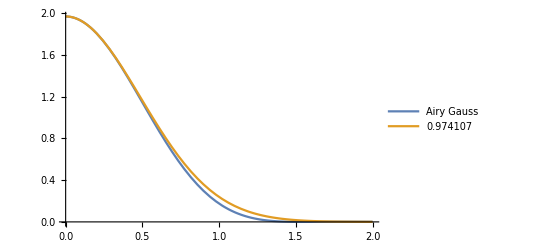

```mathematica
avals = {0.974107};
leg = Join[{"Airy Gauss"},avals];
plt=Plot[Evaluate[Join[{Series[AGterms,{x,0,100}]//Normal},(AGterms/.x-> 0)Table[Exp[(-2 x^2)/a^2],{a,avals}]]],{x,0,2},PlotLegends->leg]
```

General::munfl: -1.093×10^-41 1.62805×10^-270 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.21834×10^-43 1.08708×10^-278 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.28626×10^-45 7.25871×10^-287 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

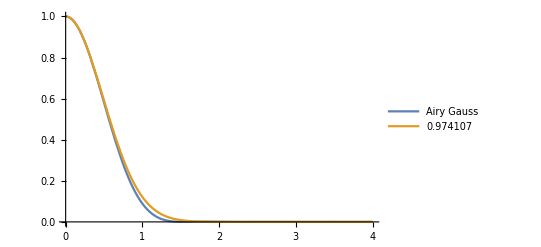

```mathematica
plt=Plot[Evaluate[Join[{AGterms/(AGterms/.x-> 0)},Table[Exp[(-2 x^2)/a^2],{a,avals}]]],{x,0,4},PlotLegends->leg]
```

```mathematica
SetDirectory[NotebookDirectory[]];
xpts = Range[0,4,0.01];
data={Table[AGterms,{x,xpts}],xpts};
Export["airygauss.csv",data];
```

Numerically

### axial expansion

```mathematica
(I+1)
```

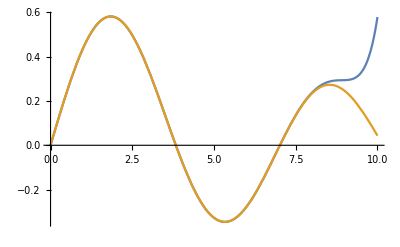

```mathematica
Plot[{Sum[(-1)^l/(2^(2l+1)(l+1)!l!)x^(2l+1),{l,0,10}],BesselJ[1,x]},{x,0,10}]
```

```mathematica
Clear[α,β,b,k,f1,f2,a,λ,w0,f]
terms=12;
A2=Sum[((-1)^l β^(2l+1))/(2^(2(l+1))l!(l+1)!)(-ⅈ α)^m/(m!)b^(2(l+m+1))/(2(m+l+1)),{m,0,terms},{l,0,terms}];
f1=f2=1;
α=k/(2 f2^2)z;
β=(a k)/f1;
b=f1/(a k)BesselJZero[1,1];
(*k =2π/λ;*)
ibrightz=Chop[Collect[((k a)/f2)^2 conj[A2]A2//ComplexExpand,z]]//N;
ibrightz=ibrightz/(%[[1]])//Expand
```

1.-(2.59936 z^2)/(a^4 k^2)+(3.28402 z^4)/(a^8 k^4)-(2.43763 z^6)/(a^12 k^6)+(1.18814 z^8)/(a^16 k^8)-(0.40904 z^10)/(a^20 k^10)+(0.104713 z^12)/(a^24 k^12)-(0.563738 z^14)/(a^28 k^14)+(1.17858 z^16)/(a^32 k^16)-(1.27328 z^18)/(a^36 k^18)+(0.833842 z^20)/(a^40 k^20)-(0.365492 z^22)/(a^44 k^22)+(0.114648 z^24)/(a^48 k^24)

Check that I correctly Taylor expanded the integral which gave the series for A2 above.

```mathematica
A22=Collect[Integrate[Series[Exp[-ⅈ α ρ^2]BesselJ[1,β ρ],{z,0,10}],{ρ,0,b}],z]//N;
Chop[Collect[((k a)/f2)^2 conj[A22]A22//ComplexExpand,z]]//N;
%/(%[[1]])//Expand
```

1.-(0.0658426 z^2 λ^2)/a^4+(0.0021071 z^4 λ^4)/a^8-(0.0000396176 z^6 λ^6)/a^12+(4.89133×10^-7 z^8 λ^8)/a^16-(4.26548×10^-9 z^10 λ^10)/a^20+(5.74738×10^-10 z^12 λ^12)/a^24

```mathematica
Clear[w,w0,R,η,λ]
zR = π w0^2/λ;
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
Eg/.ρ->0;
Series[%,{z,0,terms}]//Normal;
Collect[conj[%]%,z]
```

1-(z^2 λ^2)/(π^2 w0^4)+(z^4 λ^4)/(π^4 w0^8)-(z^6 λ^6)/(π^6 w0^12)+(z^8 λ^8)/(π^8 w0^16)-(z^10 λ^10)/(π^10 w0^20)+(z^12 λ^12)/(π^12 w0^24)-(z^14 λ^14)/(π^14 w0^28)-(z^16 λ^16)/(π^16 w0^32)+(z^18 λ^18)/(π^18 w0^36)-(z^20 λ^20)/(π^20 w0^40)+(z^22 λ^22)/(π^22 w0^44)-(z^24 λ^24)/(π^24 w0^48)+(z^26 λ^26)/(π^26 w0^52)-(z^28 λ^28)/(π^28 w0^56)+(z^30 λ^30)/(π^30 w0^60)

```mathematica
Table[π^-n//N,{n,{2,4,6,8}}]
```

{0.101321,0.010266,0.00104016,0.00010539}

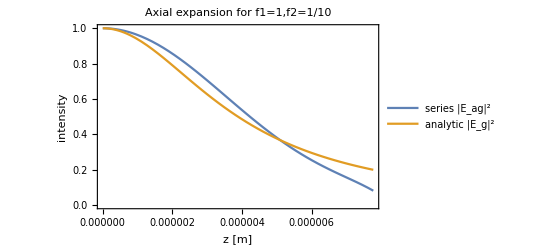

```mathematica
λ=8.08*10^-7;
w0=1*^-6;
f1=1;
f2=1/100;
a = (f1/f2)(w0/0.974);
plt=Plot[{1.-(0.06584259063048949 f1^4 z^2 λ^2)/(a^4 f2^4)+(0.0021071045764484105 f1^8 z^4 λ^4)/(a^8 f2^8)-(0.00003961760704338532 f1^12 z^6 λ^6)/(a^12 f2^12)+(4.891331404639926*^-7 f1^16 z^8 λ^8)/(a^16 f2^16)-(4.265477169147813*^-9 f1^20 z^10 λ^10)/(a^20 f2^20),1/(1+(z/zR)^2)},{z,0,2zR},PlotLegends->{"series |E_ag|^2","analytic |E_g|^2"},FrameLabel->{"z [m]","intensity"},PlotRange->{0,1},Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black,FontSize->12],PlotLabel->"Axial expansion for f1=1,f2=1/10"];
Show[plt]
```

```mathematica
Export["axial_expansion_ag_g_f1_1_f2_pt01.pdf",plt]
```

axial_expansion_ag_g_f1_1_f2_pt01.pdf

```mathematica
Clear[w0,λ,f1,f2,zR]
a=(f1/f2)w0/0.974;
(*λ = (π w0^2)/zR*)
```

```mathematica
1.-(0.06584259063048949 f1^4 z^2 λ^2)/(a^4 f2^4)+(0.0021071045764484105 f1^8 z^4 λ^4)/(a^8 f2^8)-(0.00003961760704338532 f1^12 z^6 λ^6)/(a^12 f2^12)+(4.891331404639926*^-7 f1^16 z^8 λ^8)/(a^16 f2^16)-(4.265477169147813*^-9 f1^20 z^10 λ^10)/(a^20 f2^20)
```

1.-(0.0592574 z^2 λ^2)/w0^4+(0.0017067 z^4 λ^4)/w0^8-(0.0000288799 z^6 λ^6)/w0^12+(3.20901×10^-7 z^8 λ^8)/w0^16-(2.51853×10^-9 z^10 λ^10)/w0^20

```mathematica
1/0.584847
```

1.70985

```mathematica
zpts=Range[0,5]*10^-6;
λ=8.08*10^-7;
w0=10^-6;
a=w0/0.974;
f1=1;
f2=f1;
(*numerical =Table[((k a)/f2)^2 Abs[NIntegrate[Exp[-ⅈ k/(2 f2^2)ρ^2 z]BesselJ[1,β ρ],{ρ,0,b}]]^2,{z,zpts}];*)
numerical =Table[((k a)/f2)^2 Abs[NIntegrate[Cos[ k/(2 f2^2)ρ^2 z]BesselJ[1,β ρ],{ρ,0,b},MinRecursion->10,MaxRecursion->50]-ⅈ NIntegrate[Sin[ k/(2 f2^2)ρ^2 z]BesselJ[1,β ρ],{ρ,0,b},MinRecursion->10,MaxRecursion->50]]^2,{z,zpts}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
numerical
```

{1.96773,1.89302,1.68515,1.38774,1.05833,0.751724}

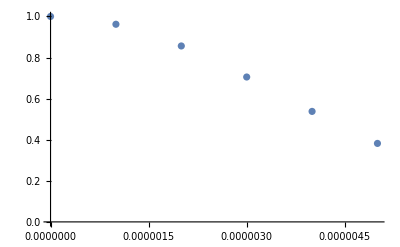

```mathematica
ListPlot[Transpose@@{{zpts,numerical/numerical[[1]]}},PlotRange->All]
```

```mathematica
Range[0,5]*10^-6
```

```mathematica
((k a)/f2)^2 Abs[NIntegrate[Exp[-ⅈ k/(2 f2^2)ρ^2 2*10^-6]BesselJ[1,β ρ],{ρ,0,b}]]^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ρ near {ρ} = {0.}. NIntegrate obtained -3.65739×10^-7-0.0000125435 ⅈ and 4.42882×10^-6 for the integral and error estimates.

0.000380895

```mathematica
f2
```

0.005

```mathematica
Plot[]
```

```mathematica
Series[(ⅇ^(-ⅈ ArcTan[(z λ)/(π w0^2)]))/(√(1+(z^2 λ^2)/(π^2 w0^4))),{z,0,4}]
```

1-(ⅈ λ z)/(π w0^2)-(λ^2 z^2)/(π^2 w0^4)+(ⅈ λ^3 z^3)/(π^3 w0^6)+(λ^4 z^4)/(π^4 w0^8)+O[z]^5

```mathematica
k
```

```mathematica
α=k/f^2 z;
β=(a k)/f;
b=f/(a k)BesselJZero[1,1]
```

```mathematica
BesselJZero[1,1]//N
```

3.83171

```mathematica
Sum[(-I)^m/(m!)x^m,{m,0,6}]
```

1-ⅈ x-x^2/2+(ⅈ x^3)/6+x^4/24-(ⅈ x^5)/120-x^6/720

```mathematica
Sum[I^m/(m!)x^m,{m,0,6}]Sum[(-I)^m/(m!)x^m,{m,0,6}]//FullSimplify
```

1+(x^8 (180-24 x^2+x^4))/518400

## dark trap

### radial expansion

#### ta=0.287 solution

```mathematica
BesselInt[b_,c_,d_,n_]:=Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}];
```

```mathematica
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ρ0,ρ2];
f1=f2=1;
tb = 1;
ta=0.287119;
b=(f1/(a k)) BesselJZero[1,1];
k =2π/λ;
(*a=w0/0.943120;*)
terms=30;
A2=-(k /f2)a (tb-ta)BesselInt[b,(ρ2 k)/f2,(a k)/f1,terms]+tb ;
idarkr=Collect[Chop[conj[A2]A2//ComplexExpand]//N,ρ2]
(*Collect[%/(%[[1]])//Expand,z]*)
idarkr/.ρ2->0
```

-(9.76327×10^-7 ρ2^2)/w0^2+(0.878703 ρ2^4)/w0^4-(0.652816 ρ2^6)/w0^6+(0.254479 ρ2^8)/w0^8-(0.0667873 ρ2^10)/w0^10+(0.0130328 ρ2^12)/w0^12-(0.00199288 ρ2^14)/w0^14+(0.000246693 ρ2^16)/w0^16-(0.0000252902 ρ2^18)/w0^18+(2.18479×10^-6 ρ2^20)/w0^20-(1.61297×10^-7 ρ2^22)/w0^22+(1.02966×10^-8 ρ2^24)/w0^24-(5.7406×10^-10 ρ2^26)/w0^26

0.

```mathematica
1/.943120
```

1.06031

```mathematica
-(1.0976432877176316*^-6 ρ2^2)/a^2+(1.11064263274065 ρ2^4)/a^4-(0.927659905532465 ρ2^6)/a^6+(0.40655208589512826 ρ2^8)/a^8-(0.11995671800479214 ρ2^10)/a^10+(0.02631692838977216 ρ2^12)/a^12-(0.004524228965597224 ρ2^14)/a^14+(0.000629631198549887 ρ2^16)/a^16-(0.00007256825104307225 ρ2^18)/a^18+(7.048090817805216*^-6 ρ2^20)/a^20-(5.849967670722265*^-7 ρ2^22)/a^22+(4.198411238482837*^-8 ρ2^24)/a^24-(2.6315770467193562*^-9 ρ2^26)/a^26+(1.4531773587501128*^-10 ρ2^28)/a^28/.ρ2->r
```

-(1.09764×10^-6 r^2)/a^2+(1.11064 r^4)/a^4-(0.92766 r^6)/a^6+(0.406552 r^8)/a^8-(0.119957 r^10)/a^10+(0.0263169 r^12)/a^12-(0.00452423 r^14)/a^14+(0.000629631 r^16)/a^16-(0.0000725683 r^18)/a^18+(7.04809×10^-6 r^20)/a^20-(5.84997×10^-7 r^22)/a^22+(4.19841×10^-8 r^24)/a^24-(2.63158×10^-9 r^26)/a^26+(1.45318×10^-10 r^28)/a^28

```mathematica
Clear[w,w0,R,η,λ]
zR = π w0^2/λ;
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
Iexac=(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2]);
Iradial=Limit[Iexac,z->0];
Series[Iradial,{ρ,0,6}]
```

ρ^4/w0^4-ρ^6/w0^6+O[ρ]^7

```mathematica
a=0.974w0;
idarkr
```

-(1.15703×10^-6 ρ2^2)/w0^2+(1.23407 ρ2^4)/w0^4-(1.08651 ρ2^6)/w0^6+(0.501932 ρ2^8)/w0^8-(0.156112 ρ2^10)/w0^10+(0.0361017 ρ2^12)/w0^12-(0.00654213 ρ2^14)/w0^14+(0.000959716 ρ2^16)/w0^16-(0.000116596 ρ2^18)/w0^18+(0.0000119369 ρ2^20)/w0^20-(1.04437×10^-6 ρ2^22)/w0^22+(7.90078×10^-8 ρ2^24)/w0^24-(5.22015×10^-9 ρ2^26)/w0^26+(3.03856×10^-10 ρ2^28)/w0^28

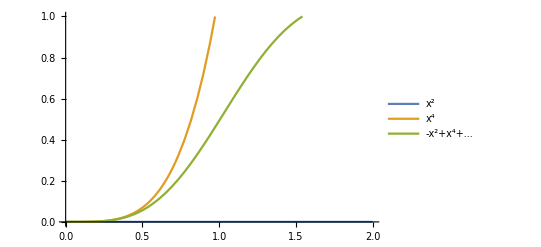

```mathematica
Plot[{1.0976432877176316*^-6 x^2,1.11064263274065 x^4,idarkr/.ρ2->x a},{x,0,2},PlotLegends->{"x^2","x^4","-x^2+x^4+..."},PlotRange->{0,1}]
```

```mathematica
a=1;
Table[idarkr,{ρ2,Range[0,0.1,0.002]}]
```

{0.,1.33796×10^-11,2.66758×10^-10,1.39983×10^-9,4.4787×10^-9,1.09957×10^-8,2.28695×10^-8,4.24443×10^-8,7.24905×10^-8,1.16204×10^-7,1.77204×10^-7,2.59538×10^-7,3.67675×10^-7,5.06509×10^-7,6.81356×10^-7,8.97957×10^-7,1.16247×10^-6,1.48149×10^-6,1.86201×10^-6,2.31146×10^-6,2.83769×10^-6,3.44896×10^-6,4.15394×10^-6,4.96175×10^-6,5.88189×10^-6,6.92429×10^-6,8.09931×10^-6,9.41768×10^-6,0.0000108906,0.0000125296,0.0000143468,0.0000163544,0.0000185654,0.0000209928,0.0000236505,0.0000265522,0.0000297126,0.0000331464,0.0000368688,0.0000408955,0.0000452424,0.000049926,0.0000549631,0.0000603709,0.0000661669,0.0000723691,0.000078996,0.0000860661,0.0000935987,0.000101613,0.00011013}

```mathematica
Range
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{}}

```mathematica
idarkr
```

-1.09764×10^-6 ρ2^2+1.11064 ρ2^4-0.92766 ρ2^6+0.406552 ρ2^8-0.119957 ρ2^10+0.0263169 ρ2^12-0.00452423 ρ2^14+0.000629631 ρ2^16-0.0000725683 ρ2^18+7.04809×10^-6 ρ2^20-5.84997×10^-7 ρ2^22+4.19841×10^-8 ρ2^24-2.63158×10^-9 ρ2^26+1.45318×10^-10 ρ2^28

```mathematica
Clear[ta,tb];
tb;
NSolve[tb-(ta-tb)(1-BesselJ[0,BesselJZero[1,1]])==0,ta](*mathematica can't do algebra. it gets this very easily solveable problem incorrect. the correct answer is ta=0.287119*)
```

{{ta→1.71288 tb}}

```mathematica
-(1. (-1. tb-1. tb (1.-1. BesselJ[0.,x])))/(1.-1. BesselJ[0.,x])//Simplify
```

(tb (-2.+1. BesselJ[0.,x]))/(-1.+1. BesselJ[0.,x])

```mathematica
(-BesselJ[0,BesselJZero[1,1]])/(1-BesselJ[0,BesselJZero[1,1]])//N
```

0.287119

```mathematica
-(tb-(ta-tb)(1-BesselJ[0,BesselJZero[1,1]]))//N
```

```mathematica
-1.+1.402759395702553 (-1.+ta)//Expand
```

-2.40276+1.40276 ta

```mathematica
BesselJ[0,BesselJZero[1,1]]//N
```

-0.402759

```mathematica
Clear[a]
Collect[-(k /f2)a BesselInt[b,(ρ2 k)/f2,(a k)/f1,terms]//N,ρ2]
ag=%/(%[[1]])//Expand
```

-1.40276+(1.47833 ρ2^2)/a^2-(0.617383 ρ2^4)/a^4+(0.141654 ρ2^6)/a^6-(0.0206802 ρ2^8)/a^8+(0.00208405 ρ2^10)/a^10-(0.000165966 ρ2^12)/a^12+(2.77008×10^-6 ρ2^14)/a^14-(2.20555×10^-6 ρ2^16)/a^16-(2.25298×10^-7 ρ2^18)/a^18-(1.12473×10^-8 ρ2^20)/a^20

1.-(1.05387 ρ2^2)/a^2+(0.44012 ρ2^4)/a^4-(0.100982 ρ2^6)/a^6+(0.0147425 ρ2^8)/a^8-(0.00148568 ρ2^10)/a^10+(0.000118314 ρ2^12)/a^12-(1.97474×10^-6 ρ2^14)/a^14+(1.5723×10^-6 ρ2^16)/a^16+(1.60611×10^-7 ρ2^18)/a^18+(8.018×10^-9 ρ2^20)/a^20

```mathematica
√1.2340663565412298
```

1.11089

```mathematica
Clear[w,w0,R,η,λ,z]
zR = π w0^2/λ;
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
Iexac=(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2]);(*exact expression for |1_E_g|^2*)
```

```mathematica
Series[1-Exp[-2 ρ^2/w0^2],{ρ,0,8}]
```

(2 ρ^2)/w0^2-(2 ρ^4)/w0^4+(4 ρ^6)/(3 w0^6)-(2 ρ^8)/(3 w0^8)+O[ρ]^9

```mathematica
model=Limit[Iexac,z->0];
NSolve[model==1/ⅇ^2,ρ,Reals]
```

{{ρ→-0.677256 √(w0^2)},{ρ→0.677256 √(w0^2)}}

```mathematica
model=Limit[Iexac,z->0]
```

ⅇ^(-2000000000000 ρ^2) (-1+ⅇ^(1000000000000 ρ^2))^2

```mathematica
ⅇ^(-(2 ρ^2)/w0^2) (-1+ⅇ^(ρ^2/w0^2))^2
```

1+ⅇ^(-2000000000000 ρ^2)-2 ⅇ^(-1000000000000 ρ^2)

```mathematica
w0=10^-6;
f=model-1/ⅇ^2//N;
df=D[f,ρ];
x0=6.9*10^-7;
xNext[x_]:=x0-(f/.ρ->x)/(df/.ρ->x)//N;
xNext[x0]
```

6.77446×10^-7

```mathematica
xNext[%]
```

6.88779×10^-7

```mathematica
f/.ρ->6.7725*10^-7
```

-3.5267×10^-6

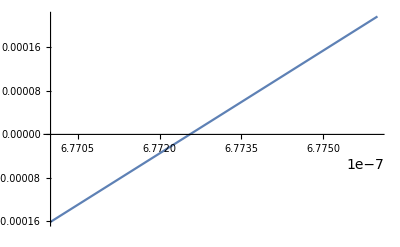

```mathematica
Plot[model-1/ⅇ^2,{ρ,6.77*10^-7,6.776*10^-7}]
```

Least squares minimization to find an ideal w0 parameter up on an interval of rho from 0 to rho_1/e found above.

```mathematica
xmax=(6.7725*10^-7)/10^-6;
xpts = Range[0,xmax,xmax/10];
```

```mathematica
model
```

ⅇ^(-(2 ρ^2)/w0^2) (-1+ⅇ^(ρ^2/w0^2))^2

```mathematica
(*make sure that both idarkr and model are fully symbolic at this point.*)
a = u w0;
f =Sum[((idarkr/.ρ2->w0 ρ)-model/.w0->1)^2/.ρ->xpts[[i]],{i,Range[10]}];
df =D[f,u];
u0 = 1.069;
xNext[x_]:=u0-(f/.u->x)/(df/.u->x)//N;
xNext[u0]
```

1.05575

```mathematica
xNext[%]
```

1.06031

```mathematica
idarkr
```

-7.15106×10^-7 ρ^2+0.471403 ρ^4-0.256517 ρ^6+0.0732406 ρ^8-0.0140789 ρ^10+0.00201228 ρ^12-0.000225376 ρ^14+0.0000204342 ρ^16-1.53436×10^-6 ρ^18+9.70869×10^-8 ρ^20-5.2499×10^-9 ρ^22+2.45466×10^-10 ρ^24-1.00238×10^-11 ρ^26+3.60614×10^-13 ρ^28

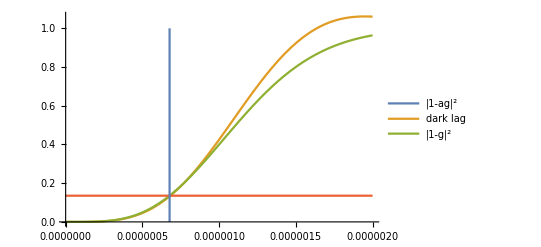

1+(ⅇ^(-(2000000000000 ρ^2)/(1+(640000000000 z^2)/π^2)))/(1+(640000000000 z^2)/π^2)-(2 ⅇ^(-(1000000000000 ρ^2)/(1+(640000000000 z^2)/π^2)) Cos[(1250000 π ρ^2)/((1+π^2/(640000000000 z^2)) z)-ArcTan[(800000 z)/π]])/(√(1+(640000000000 z^2)/π^2))

```mathematica
a=1.06031w0;
w0=10^-6;
λ=8*^-7;
Show[Plot[{(1-ag)^2/.ρ2->ρ,idarkr/.ρ2->ρ,model,1/ⅇ^2},{ρ,0,2w0},PlotLegends->{"|1-ag|^2","dark Iag","|1-g|^2"}],ListPlot[{{6.7725*10^-7,0},{6.7725*10^-7,1}},Joined->True]]
```

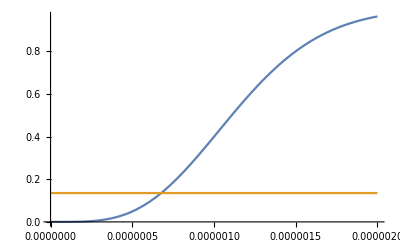

```mathematica
Plot[{model,1/ⅇ^2},{ρ,0,2w0}]
```

#### ta=0 solution

The trap should go dark for any zero of J0. test this for the first few zeroes.

```mathematica
BesselJZero[0,1]//N
```

2.40483

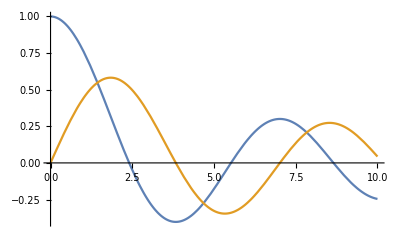

```mathematica
Plot[{BesselJ[0,x],BesselJ[1,x]},{x,0,10}]
```

```mathematica
BesselInt[b_,c_,d_,n_]:=Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}];
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ρ0,ρ2];
f1=f2=1;
tb = 1;
ta=0;
b=(f1/(a k)) BesselJZero[0,n];(*this is the primary difference from the ta=0.287 case*)
k =2π/λ;
a=w0/0.943120;
terms={20,30,50};
nsteps = Range[1];
showterms=30 ;
idarktable = {};
For[i=1,i<Length[nsteps]+1,i++,
A2=-(k /f2)a (tb-ta)BesselInt[b,(ρ2 k)/f2,(a k)/f1,terms[[i]]]+tb /.n->nsteps[[i]];
idarkr=Collect[Chop[conj[A2]A2//ComplexExpand]//N,ρ2];
Print["first several terms(n=",nsteps[[i]],"):",Series[idarkr/.ρ2->r,{r,0,terms[[i]]}]//Normal];
(*Print["the whole expansion(n=",nsteps[[i]],"):",Collect[idarkr/.ρ2->r,r]//Normal];*)
AppendTo[idarktable,idarkr];
]
(*Collect[%/%[[1]]//Expand,z]*)
```

first several terms(n=1):(2.6249×10^-9 r^20)/w0^20-(6.56289×10^-8 r^18)/w0^18+(1.36501×10^-6 r^16)/w0^16-(0.000023168 r^14)/w0^14+(0.000313038 r^12)/w0^12-(0.00325258 r^10)/w0^10+(0.0246039 r^8)/w0^8-(0.122244 r^6)/w0^6+(0.308288 r^4)/w0^4

```mathematica
idarktable[[2]]
```

-1.81386×10^-13-3.63798×10^-12 ρ2^2+0.881992 ρ2^4-5.83686 ρ2^6+14.2961 ρ2^8-17.2867 ρ2^10+13.0202 ρ2^12-6.88739 ρ2^14+2.743 ρ2^16-0.860081 ρ2^18+0.219033 ρ2^20-0.0463591 ρ2^22+0.00830172 ρ2^24-0.00127595 ρ2^26+0.000170322 ρ2^28-0.0000199438 ρ2^30+2.06614×10^-6 ρ2^32-1.90788×10^-7 ρ2^34+1.58058×10^-8 ρ2^36-1.1816×10^-9 ρ2^38+8.0124×10^-11 ρ2^40-4.95122×10^-12 ρ2^42+2.79997×10^-13 ρ2^44-1.45464×10^-14 ρ2^46+6.96693×10^-16 ρ2^48-3.08613×10^-17 ρ2^50+1.26814×10^-18 ρ2^52-4.8472×10^-20 ρ2^54+1.72782×10^-21 ρ2^56-5.75734×10^-23 ρ2^58+1.79731×10^-24 ρ2^60-5.26752×10^-26 ρ2^62+1.45216×10^-27 ρ2^64-3.77259×10^-29 ρ2^66+9.25192×10^-31 ρ2^68-2.14534×10^-32 ρ2^70+4.71083×10^-34 ρ2^72-9.80993×10^-36 ρ2^74+1.94×10^-37 ρ2^76-3.64817×10^-39 ρ2^78+6.53161×10^-41 ρ2^80-1.11464×10^-42 ρ2^82+1.81491×10^-44 ρ2^84-2.82222×10^-46 ρ2^86+4.19529×10^-48 ρ2^88-5.96945×10^-50 ρ2^90+8.14601×10^-52 ρ2^92-1.06885×10^-53 ρ2^94+1.35436×10^-55 ρ2^96-1.64766×10^-57 ρ2^98+2.04533×10^-59 ρ2^100-1.76403×10^-61 ρ2^102+5.07645×10^-63 ρ2^104+8.03479×10^-65 ρ2^106+3.7406×10^-66 ρ2^108+8.34869×10^-68 ρ2^110+1.5836×10^-69 ρ2^112+1.94535×10^-71 ρ2^114+1.57482×10^-73 ρ2^116+6.50009×10^-76 ρ2^118+9.91116×10^-79 ρ2^120

General::munfl: 1.72503×10^-32 1.8615×10^-285 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -3.55792×10^-34 7.86045×10^-294 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.94914×10^-36 3.31919×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

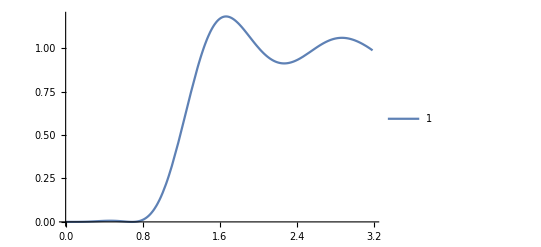

```mathematica
a=1.06031;
Plot[Evaluate[idarktable[[2]]],{ρ2,0,3a},PlotLegends->nsteps]
```

```mathematica
Length[xpts]
```

101

```mathematica
xpts = Range[0,2,0.02];
ypts2 = Table[idarktable[[2]],{ρ2,xpts}];
```

General::munfl: -1.75042×10^-75 3.48449×10^-235 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.29717×10^-77 1.3938×10^-238 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -2.93179×10^-79 5.57519×10^-242 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

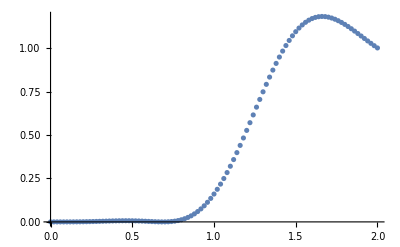

```mathematica
ListPlot[Transpose@@{{xpts,ypts2}}]
```

```mathematica
ypts2
```

{-1.81386×10^-13,1.11386×10^-7,1.76961×10^-6,8.85339×10^-6,0.0000275202,0.0000657613,0.00013281,0.000238433,0.000392139,0.000602344,0.000875551,0.00121556,0.00162281,0.00209379,0.00262072,0.00319138,0.00378919,0.00439357,0.00498056,0.00552368,0.00599507,0.00636688,0.00661283,0.00670991,0.00664026,0.00639302,0.00596624,0.00536867,0.0046214,0.00375934,0.00283239,0.00190628,0.00106309,0.000401227,0.0000351194,0.0000942926,0.000722058,0.00207371,0.00431427,0.00761585,0.0121546,0.0181075,0.0256486,0.0349454,0.0461553,0.0594215,0.0748695,0.0926037,0.112704,0.135224,0.160186,0.187582,0.217373,0.249485,0.283809,0.320208,0.358508,0.39851,0.439984,0.482679,0.526321,0.57062,0.615272,0.659965,0.704385,0.748217,0.791151,0.832888,0.873142,0.911647,0.948156,0.982448,1.01433,1.04364,1.07024,1.09403,1.11494,1.13294,1.14803,1.16023,1.16959,1.17621,1.18019,1.18166,1.18076,1.17768,1.17259,1.16569,1.15716,1.14723,1.13608,1.12394,1.11099,1.09745,1.0835,1.06931,1.05508,1.04094,1.02706,1.01357,1.00059}

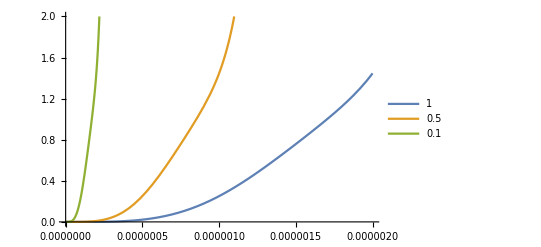

```mathematica
Clear[a]
asteps = {1,0.5,0.1};
Plot[Evaluate[Table[idarktable[[1]]/.a->i*10^-6,{i,asteps}]],{ρ2,0,2*10^-6},PlotLegends->asteps,PlotRange->{0,2}]
```

Match the ta=0 solution to the Gaussian equivalent solution

```mathematica
model = ⅇ^(-(2 ρ^2)/w0^2) (-1+ⅇ^(ρ^2/w0^2))^2
xmax=(6.7725*10^-7)/10^-6;
xpts = Range[0,xmax,xmax/20];
```

ⅇ^(-(2 ρ^2)/w0^2) (-1+ⅇ^(ρ^2/w0^2))^2

```mathematica
(*make sure that both idarkr and model are fully symbolic at this point.*)
Clear[w0]
a = u w0;
f =Sum[((idarktable[[2]]/.ρ2->w0 ρ)-model/.w0->1)^2/.ρ->xpts[[i]],{i,Range[20]}];
df =D[f,u];
u0 = 0.732;
xNext[x_]:=u0-(f/.u->x)/(df/.u->x)//N;
xNext[u0]
```

0.663235

```mathematica
trials={}
xtry=u0
Do[
xtry=xNext[xtry];
AppendTo[trials,xtry];
,1000]
```

{}

0.732

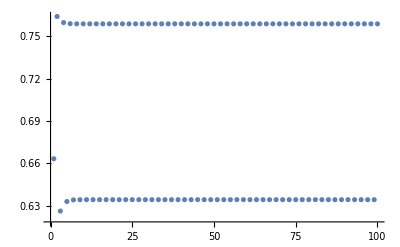

```mathematica
ListPlot[trials[[;;100]]]
```

```mathematica
trials[[-1]]
```

0.755981

General::munfl: (4.08571×10^-11)^30 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.08571×10^-11)^32 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.08571×10^-11)^34 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

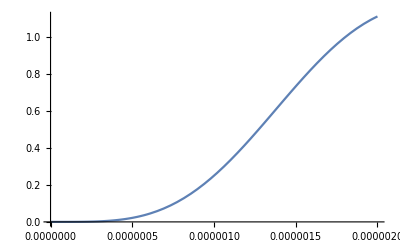

```mathematica
a=10^-6;
Plot[idarktable[[1]],{ρ2,0,2a}]
```

```mathematica
model
```

ⅇ^(-2 ρ^2) (-1+ⅇ^(ρ^2))^2

General::munfl: 3.42224×10^-29 1.32176×10^-281 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -7.90808×10^-31 2.20642×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.72503×10^-32 3.68318×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

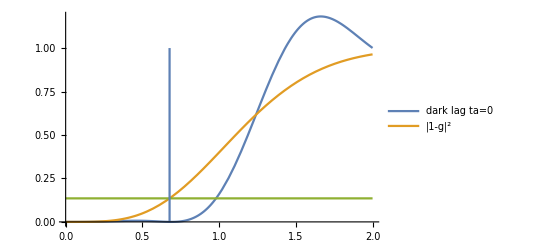

```mathematica
a=1.06031;(*0.8622086026977531*)
w0=1;
λ=8*^-7;
Show[Plot[{idarktable[[2]]/.ρ2->ρ,model,1/ⅇ^2},{ρ,0,2w0},PlotLegends->{"dark Iag ta=0","|1-g|^2"}],ListPlot[{{.67725,0},{.67725,1}},Joined->True]](*PlotRange->{{0.6,0.7},{1/ⅇ^2-0.5,1/ⅇ^2+0.5}}*)
```

General::munfl: -6.31203×10^-19 2.20642×10^-290 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.15911×10^-20 3.68318×10^-299 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.49497×10^-21 6.14836×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

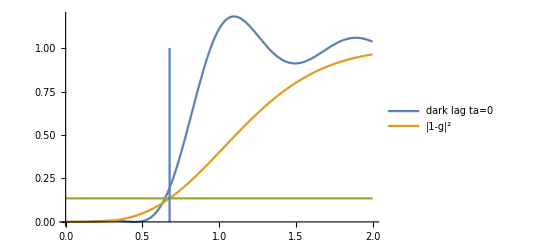

```mathematica
a=0.7w0;(*0.8622086026977531*)
w0=1;
λ=8*^-7;
Show[Plot[{idarktable[[2]]/.ρ2->ρ,model,1/ⅇ^2},{ρ,0,2w0},PlotLegends->{"dark Iag ta=0","|1-g|^2"}],ListPlot[{{.67725,0},{.67725,1}},Joined->True]](*PlotRange->{{0.6,0.7},{1/ⅇ^2-0.5,1/ⅇ^2+0.5}}*)
```

### axial expansion

#### ta=0.287 solution

Assuming the input plane wave was infinite in extent, it transforms to a delta function in the Fourier plane and back to an infinite plane wave in the output plane. Then the output field is a plane wave, which does not change intensity as it propagates.

```mathematica
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ta,tb];
terms=10;
A2 =-ⅈ k/f2 a(tb-ta)Sum[(-1)^l/(2^(2l+1)l!(l+1)!)(-ⅈ α)^m/(m!)β^(2l+1)/(2(m+l+1))b^(2(l+m+1)),{m,0,terms},{l,0,terms}]+ ⅈ tb;
f1=f2;
α=k/(2 f2^2)z;
β=(a k)/f1;
b=f1/(a k)BesselJZero[1,1];
a ;(*=(f1/f2)w0/0.974*);
tb=1;
ta=(*0.287119;*)
(*k=2π/λ;*)
```

```mathematica
idarkz=Collect[Chop[conj[A2]A2 //ComplexExpand],z]
(*CoefficientList[idarkr=Collect[%/(%[[1]]),z],z]*)
(*CoefficientList[%,z]*)
```

(4.44257 z^2)/(a^4 k^2)-(8.03602 z^4)/(a^8 k^4)+(7.7908 z^6)/(a^12 k^6)-(4.69372 z^8)/(a^16 k^8)+(1.92573 z^10)/(a^20 k^10)+(2.17585 z^12)/(a^24 k^12)-(4.49972 z^14)/(a^28 k^14)+(4.81662 z^16)/(a^32 k^16)-(3.12978 z^18)/(a^36 k^18)+(1.36279 z^20)/(a^40 k^20)

Check that I correctly Taylor expanded the integral which gave the series for A2 above.

```mathematica
ta=0.287119;
A22=-ⅈ((k a)/f2)(tb-ta)Collect[Integrate[Series[Exp[-ⅈ α ρ^2]BesselJ[1,β ρ],{z,0,terms}],{ρ,0,b}],z]+ⅈ tb//N;
Chop[Collect[conj[A22]A22//ComplexExpand,z]]//N
```

(4.44257 z^2)/(a^4 k^2)-(8.03602 z^4)/(a^8 k^4)+(7.7908 z^6)/(a^12 k^6)-(4.69372 z^8)/(a^16 k^8)+(1.92573 z^10)/(a^20 k^10)+(2.17585 z^12)/(a^24 k^12)-(4.49972 z^14)/(a^28 k^14)+(4.81662 z^16)/(a^32 k^16)-(3.12978 z^18)/(a^36 k^18)+(1.36279 z^20)/(a^40 k^20)

```mathematica
Clear[w,w0,R,η,λ]
zR = π w0^2/λ;
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
idarkg = (1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2]); (*exact formula for |1-Eg|^2*)
```

```mathematica
Table[π^-n//N,{n,{2,4,6,8}}]
```

{0.101321,0.010266,0.00104016,0.00010539}

-5.1962×10^-14

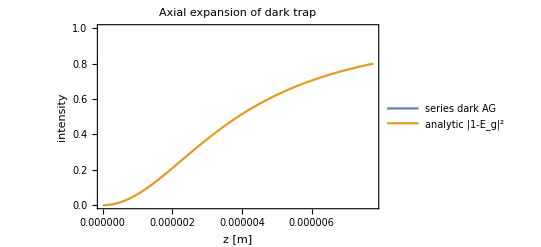

```mathematica
λ=8.08*10^-7;
w0=1*^-6;
f1=1;
f2=1;
a = (f1/f2)(w0/0.974);
fudge=-5.1961965913882566*^-14
plt=Plot[{idarkr,idarkg/.ρ->0},{z,0,2zR},PlotLegends->{"series dark AG","analytic |1-E_g|^2"},FrameLabel->{"z [m]","intensity"},PlotRange->{0,1},Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black,FontSize->12],PlotLabel->"Axial expansion of dark trap"];
Show[plt]
```

```mathematica
idarkr
```

-9.53722×10^-17-3.306×10^10 z^2+8.90037×10^20 z^4-1.28425×10^31 z^6+1.15155×10^41 z^8-8.52526×10^50 z^10

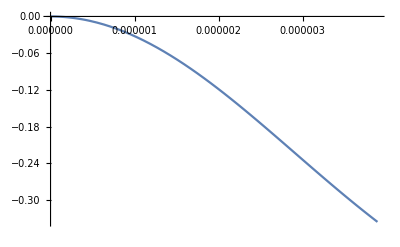

```mathematica
Plot[idarkr,{z,0,zR},PlotRange->All]
```

```mathematica
Export["axial_expansion_dark_ag_g_f1_1_f2_pt01.pdf",plt]
```

axial_expansion_ag_g_f1_1_f2_pt01.pdf

```mathematica
Clear[w0,λ,f1,f2,zR]
a=(f1/f2)w0/0.974;
(*λ = (π w0^2)/zR*)
```

```mathematica
1.-(0.06584259063048949 f1^4 z^2 λ^2)/(a^4 f2^4)+(0.0021071045764484105 f1^8 z^4 λ^4)/(a^8 f2^8)-(0.00003961760704338532 f1^12 z^6 λ^6)/(a^12 f2^12)+(4.891331404639926*^-7 f1^16 z^8 λ^8)/(a^16 f2^16)-(4.265477169147813*^-9 f1^20 z^10 λ^10)/(a^20 f2^20)
```

1.-(0.0592574 z^2 λ^2)/w0^4+(0.0017067 z^4 λ^4)/w0^8-(0.0000288799 z^6 λ^6)/w0^12+(3.20901×10^-7 z^8 λ^8)/w0^16-(2.51853×10^-9 z^10 λ^10)/w0^20

```mathematica
1/0.584847
```

1.70985

#### ta=0 solution

```mathematica
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ρ0,ρ2];
f1=f2=1;
tb = 1;
ta=0;
α=k/(2 f2^2)z;
β=(a k)/f1;
a=w0/0.943120;
k=2π/λ;
λ=π w0^2/zR;
b=(f1/(a k)) BesselJZero[0,n];(*this is the primary difference from the ta=0.287 case*)
terms={10,20,30};
nsteps = Range[1];
(*showterms=20;*)
idarktable = {};
For[i=1,i<Length[nsteps]+1,i++,
A2=-k/f2 a(tb-ta)Sum[(-1)^l/(2^(2l+1)l!(l+1)!)(-ⅈ α)^m/(m!)β^(2l+1)/(2(m+l+1))b^(2(l+m+1)),{m,0,terms[[i]]},{l,0,terms[[i]]}]+ tb/.n->nsteps[[i]];
idarkz=Collect[Chop[conj[A2]A2//ComplexExpand]//N,z];
Print["first several terms (n=",nsteps[[i]],"):",Series[idarkz,{z,0,terms[[i]]}]//Normal];
AppendTo[idarktable,idarkz];
]
(*Collect[%/%[[1]]//Expand,z]*)
```

first few several(n=1):(3.72926×10^-7 z^10)/zR^10-(0.0000246237 z^8)/zR^8+(0.00106033 z^6)/zR^6-(0.0264412 z^4)/zR^4+(0.308288 z^2)/zR^2

General::munfl: 1/((7.77622×10^6)^46) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^48) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^50) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

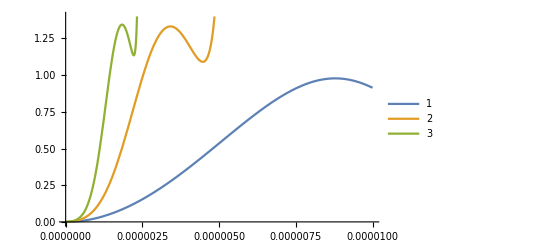

```mathematica
a=10^-6;
k = 2π/(8.08*^-7);
Plot[Evaluate[idarktable[[;;3]]],{z,0,10a},PlotLegends->nsteps,PlotRange->{0,1.4}]
```

General::munfl: 1/((7.77622×10^6)^46) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^48) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^50) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

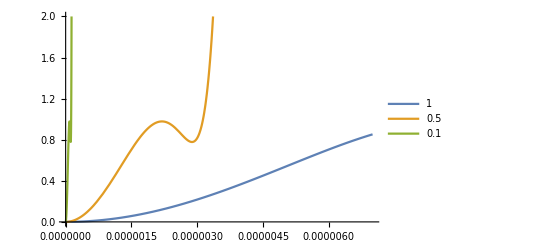

```mathematica
Clear[a]
asteps = {1,0.5,0.1};
Plot[Evaluate[Table[idarktable[[1]]/.a->i*10^-6,{i,asteps}]],{z,0,7*10^-6},PlotLegends->asteps,PlotRange->{0,2}]
```

#### ta=0.7 solution

```mathematica
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ρ0,ρ2,zR];
(*f1=f2=1;*)
f1=0.5;
f2=0.05;
tb = 1;
ta=0.7;
α=k/(2 f2^2)z;
β=(a k)/f1;
a=w0/0.943120;
k=2π/λ;
λ=π w0^2/zR;
u=0.4;
b=u(f1/(a k)) BesselJZero[1,1];
terms={10,20,30};
nsteps = Range[1];
ϕ=160/180 π;
(*showterms=20;*)
idarktable = {};
For[i=1,i<Length[nsteps]+1,i++,
A2=-k/f2 a(tb-ta Exp[-ⅈ ϕ])Sum[(-1)^l/(2^(2l+1)l!(l+1)!)(-ⅈ α)^m/(m!)β^(2l+1)/(2(m+l+1))b^(2(l+m+1)),{m,0,terms[[i]]},{l,0,terms[[i]]}]+ tb;
idarkz=Collect[Chop[conj[A2]A2//ComplexExpand]//N,z];
Print["first several terms (n=",nsteps[[i]],"):",Series[idarkz,{z,0,terms[[i]]}]//Normal];
AppendTo[idarktable,idarkz];
]
(*Collect[%/%[[1]]//Expand,z]*)
```

first several terms (n=1):56.1762+((1.06776×10^10+0.00195313 ⅈ) z^10)/zR^10-((1.69652×10^9-0.000488281 ⅈ) z^9)/zR^9-(7.90283×10^7 z^8)/zR^8+((5.63283×10^7+7.62939×10^-6 ⅈ) z^7)/zR^7-(1.18381×10^7 z^6)/zR^6-(1.16811×10^6 z^5)/zR^5+((539978.-9.31323×10^-10 ⅈ) z^4)/zR^4+(13084.8 z^3)/zR^3-(9217.25 z^2)/zR^2-(60.084 z)/zR

```mathematica
(1.6965247603274212*^-10 z^9)/zR^9-(2.0379185702374738*^-8 z^8)/zR^8+(5.632834961423147*^-8 z^7)/zR^7+(5.282186393497955*^-6 z^6)/zR^6-(0.000011681050357889488 z^5)/zR^5-(0.0007886839899290503 z^4)/zR^4+(0.0013084817816530528 z^3)/zR^3+(0.05424902429971697 z^2)/zR^2-(0.0600839568851754 z)/zR
```

```mathematica
a=10^-6;
k = 2π/(8.08*^-7);
Plot[Evaluate[idarktable[[;;3]]],{z,0,10a},PlotLegends->nsteps,PlotRange->{0,1.4}]
```

General::munfl: 1/((7.77622×10^6)^46) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^48) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^50) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[a]
asteps = {1,0.5,0.1};
Plot[Evaluate[Table[idarktable[[1]]/.a->i*10^-6,{i,asteps}]],{z,0,7*10^-6},PlotLegends->asteps,PlotRange->{0,2}]
```

General::munfl: 1/((7.77622×10^6)^46) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^48) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/((7.77622×10^6)^50) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

### sensitivity to trap parameters

For what parameters b, ta, and t (phase difference) can the trap center intensity be zero? Set tb = 1.

```mathematica
t=0;
a=BesselJ[0,BesselJZero[1,1]];
ta=(Cos[t]^2 a (a-1)+√((Cos[t]^4-1)a^2(a-1)^2))/(a-1)^2//N
```

```mathematica
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ρ0,ρ2,ta,tb];
BesselInt[b_,c_,d_,n_]:=Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}];
f1=f2=1;
tb = 1;
ta=0.287119;
b=(f1/(a k)) u BesselJZero[1,1];
k =2π/λ;
terms=10;
A2=-(k /f2)a (tb-ta Exp[-ⅈ ϕ])BesselInt[b,(ρ2 k)/f2,(a k)/f1,terms]+tb ;
idarkr=Collect[Chop[conj[A2]A2//ComplexExpand]//N,ρ2];
(*Collect[%/(%[[1]])//Expand,z]*)
centerI=idarkr/.ρ2->0
0.
```

1.-7.34099 u^2+20.2088 u^4-27.4727 u^6+22.0583 u^8-11.659 u^10+4.35866 u^12-1.21271 u^14+0.260815 u^16-0.0446486 u^18+0.00622753 u^20-0.000721293 u^22+0.0000704774 u^24-5.88708×10^-6 u^26+4.25074×10^-7 u^28-2.67487×10^-8 u^30+1.47228×10^-9 u^32-7.06873×10^-11 u^34+2.93206×10^-12 u^36-1.03349×10^-13 u^38+3.01408×10^-15 u^40-6.89293×10^-17 u^42+1.04547×10^-18 u^44+2.10774 u^2 Cos[ϕ]-9.67054 u^4 Cos[ϕ]+14.987 u^6 Cos[ϕ]-12.4858 u^8 Cos[ϕ]+6.66845 u^10 Cos[ϕ]-2.5002 u^12 Cos[ϕ]+0.696181 u^14 Cos[ϕ]-0.149758 u^16 Cos[ϕ]+0.0256384 u^18 Cos[ϕ]-0.00357607 u^20 Cos[ϕ]+0.000414193 u^22 Cos[ϕ]-0.0000404708 u^24 Cos[ϕ]+3.38059×10^-6 u^26 Cos[ϕ]-2.44094×10^-7 u^28 Cos[ϕ]+1.53601×10^-8 u^30 Cos[ϕ]-8.45438×10^-10 u^32 Cos[ϕ]+1.11064 u^4 Cos[ϕ]^2-2.03829 u^6 Cos[ϕ]^2+1.76648 u^8 Cos[ϕ]^2-0.953505 u^10 Cos[ϕ]^2+0.358539 u^12 Cos[ϕ]^2-0.0999142 u^14 Cos[ϕ]^2+0.0214975 u^16 Cos[ϕ]^2-0.00368056 u^18 Cos[ϕ]^2+0.000513376 u^20 Cos[ϕ]^2-0.0000594613 u^22 Cos[ϕ]^2+5.80997×10^-6 u^24 Cos[ϕ]^2-4.85315×10^-7 u^26 Cos[ϕ]^2+3.5042×10^-8 u^28 Cos[ϕ]^2-2.20509×10^-9 u^30 Cos[ϕ]^2+1.21371×10^-10 u^32 Cos[ϕ]^2+1.11064 u^4 Sin[ϕ]^2-2.03829 u^6 Sin[ϕ]^2+1.76648 u^8 Sin[ϕ]^2-0.953505 u^10 Sin[ϕ]^2+0.358539 u^12 Sin[ϕ]^2-0.0999142 u^14 Sin[ϕ]^2+0.0214975 u^16 Sin[ϕ]^2-0.00368056 u^18 Sin[ϕ]^2+0.000513376 u^20 Sin[ϕ]^2-0.0000594613 u^22 Sin[ϕ]^2+5.80997×10^-6 u^24 Sin[ϕ]^2-4.85315×10^-7 u^26 Sin[ϕ]^2+3.5042×10^-8 u^28 Sin[ϕ]^2-2.20509×10^-9 u^30 Sin[ϕ]^2+1.21371×10^-10 u^32 Sin[ϕ]^2

0.

```mathematica
(*plotting the trap profiles*)
```

```mathematica
Clear[α,β1,β2,b,k,f1,f2,a,λ,w0,f,ρ0,ρ2,ta,tb,ϕ];
BesselInt[b_,c_,d_,n_]:=Sum[(-1)^j/(j!(j+1)!(2j+2))Hypergeometric2F1[-j,-1-j,1,c^2/d^2] b^(2+2j)(d/2)^(1+2j),{j,0,n}];
f1=f2=1;
tb = 1;
(*ta=0.287119;*)
(*b=(f1/(a k)) u BesselJZero[1,1];*)
(*k =2π/λ;*)
terms=30;
A2=-(k /f2)a (tb-ta Exp[-ⅈ ϕ])BesselInt[b,(ρ2 k)/f2,(a k)/f1,terms]+tb ;
idarkr=Collect[Chop[conj[A2]A2//ComplexExpand]//N,ρ2];
c2 = (Series[idarkr,{ρ2,0,2}]//Normal)[[-1]]/.ρ2->1;
(*Collect[%/(%[[1]])//Expand,z]*)
(*Series[idarkr,{ρ2,0,2}]//Normal*)
(*centerI=idarkr/.ρ2->0*)
```

```mathematica
(*when is the quadratic coefficient non-zero?*)
a=0.974*10^-6;
k = 2π/(8.08*10^-7);
b = u(f1/(a k)) BesselJZero[1,1];
ta=0.7;
(*data=Table[c2,{ϕ,0,π,π/100},{u,0.3,1,1/100}];
data=%/Max[%];*)
(*ListContourPlot[data,PlotLegends->Automatic,PlotRange->All,Contours->30,PlotLabel->"Quadratic coefficient, ta=0.7",FrameLabel->{"iris radius","ϕ"}]*)
c2table = Table[c2,{u,0,1,1/100},{ϕ,0,π,π/100}];
(*ContourPlot[c2,{u,0.3,1},{ϕ,0,π},PlotLegends->Automatic,PlotRange->All,Contours->30,PlotLabel->"Quadratic coefficient, ta=0.7",FrameLabel->{"iris radius","ϕ"}]*)
```

General::munfl: -4.33085×10^-44 3.13757×10^-265 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.03925×10^-47 2.97654×10^-277 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.37138×10^-49 2.82377×10^-289 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

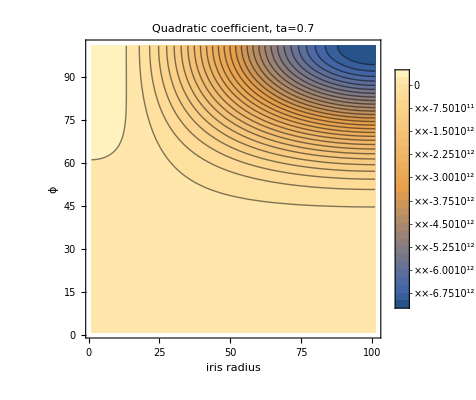

```mathematica
ListContourPlot[c2table,Contours->30,PlotLegends->Automatic,PlotRange->All,Contours->30,PlotLabel->"Quadratic coefficient, ta=0.7",FrameLabel->{"iris radius","ϕ"}]
```

```mathematica
Table[{i,j},{i,Range[3]},{j,Range[3]}]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}},{{3,1},{3,2},{3,3}}}

```mathematica
c2table[[1,50]]
```

0.

```mathematica
Image[c2table]
```

-Graphics-

```mathematica
(*Export["quad_ta_root49_phi_0_to_100_u_0_to_1.csv",c2table]*)
```

quad_ta_root49_phi_0_to_100_u_0_to_1.csv

General::munfl: -4.33085×10^-44 3.13757×10^-265 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.03925×10^-47 2.97654×10^-277 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.37138×10^-49 2.82377×10^-289 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

General::munfl: -4.33085×10^-44 3.13757×10^-265 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 8.03925×10^-47 2.97654×10^-277 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.37138×10^-49 2.82377×10^-289 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

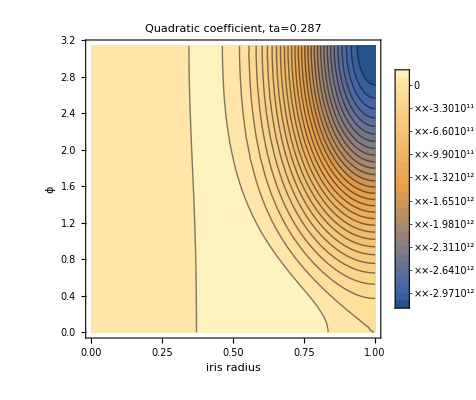

```mathematica
(*when is the quadratic coefficient non-zero?*)
a=0.974*10^-6;
k = 2π/(8.08*10^-7);
b = u(f1/(a k)) BesselJZero[1,1];
ta=0.287;
data=Table[c2,{ϕ,0,π,π/100},{u,0,1,1/100}];
data=%/Max[%];
(*ListContourPlot[data,PlotLegends->Automatic,PlotRange->All,Contours->30,PlotLabel->"Quadratic coefficient, ta=0.287",FrameLabel->{"iris radius","ϕ"}]*)
ContourPlot[c2,{u,0,1},{ϕ,0,π},PlotLegends->Automatic,PlotRange->All,Contours->30,PlotLabel->"Quadratic coefficient, ta=0.287",FrameLabel->{"iris radius","ϕ"}]
```

iris radius (dimensionless):

0.4

General::munfl: (7.77622×10^-8)^44 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (7.77622×10^-8)^46 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -1.7507×10^-46 2.97654×10^-277 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

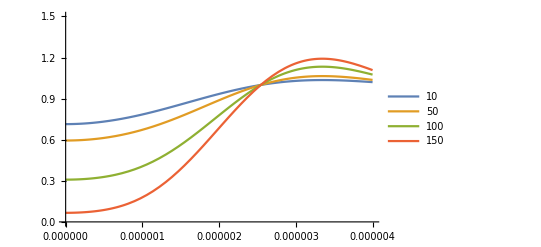

```mathematica
Clear[ϕ,b,u]
a=0.974*10^-6;
k = 2π/(8.08*10^-7);
"iris radius (dimensionless):"
u=0.4
b = u(f1/(a k)) BesselJZero[1,1];
phases = {10,50,100,150};
Plot[Evaluate[Table[idarkr/.{ta->0.7,ϕ->π/180 deg},{deg,phases}]],{ρ2,0,4*10^-6},PlotLegends->phases,PlotRange->{0,1.5}]
```

General::munfl: -1.7507×10^-46 2.97654×10^-277 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.97609×10^-49 2.82377×10^-289 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -4.66651×10^-52 2.67885×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

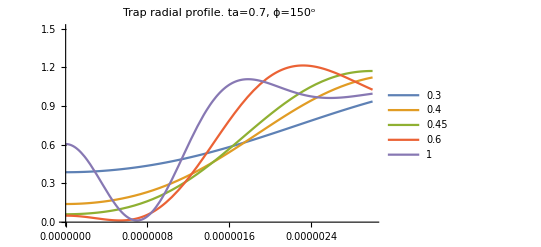

```mathematica
Clear[ϕ,b,u]
a=0.974*10^-6;
k = 2π/(8.08*10^-7);
uvals = {0.3,0.4,0.45,0.6,1};
ϕ=π/180 150;
Plot[Evaluate[Table[idarkr/.{ta->0.7,b->u(f1/(a k)) BesselJZero[1,1]},{u,uvals}]],{ρ2,0,3*10^-6},PlotLegends->uvals,PlotRange->{0,1.5},PlotLabel->"Trap radial profile. ta=0.7, ϕ=150^o"]
```

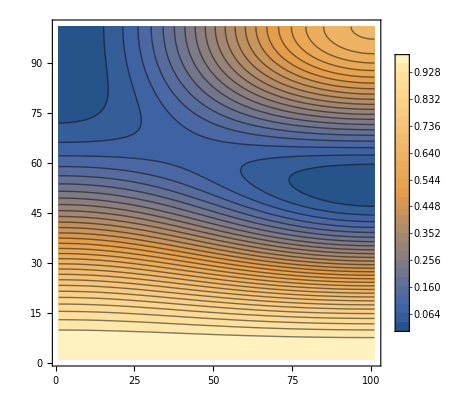

```mathematica
data=Table[centerI,{ϕ,0,π,π/100},{u,0,1,1/100}];
ListContourPlot[data,PlotLegends->Automatic,PlotRange->All,Contours->30]
```

```mathematica
(*Export[FileNameJoin[{imagedir,"ta_287119_phi_0_to_100_u_0_to_1.csv"}],data]*)
```

C:\Users\prest\OneDrive\Documents\amo-mathematica\optics\images\ta_287119_phi_0_to_100_u_0_to_1.csv

```mathematica
centerI/.{u->1,ta->0.287119}
```

2.65224×10^-13

```mathematica
α =BesselJ[0,u BesselJZero[1,1]];
(Cos[ϕ]α(α-1)+√((Cos[ϕ]^2-1)α^2(α-1)^2))/(α-1)^2/.{ϕ->100/180 π,u->0.25}
```

0.628127+3.56229 ⅈ

```mathematica
ListContourPlot[Table[,{u,10^-6,1,1/25},{ϕ,0,π,π/25}]]
```

-Graphics-

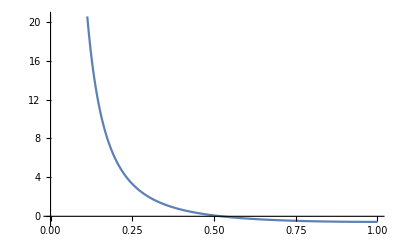

```mathematica
Plot[((α Cos[ϕ])/(-1+α)+(√(-α^2+α^2 Cos[ϕ]^2))/(-1+α)-ta)/.{ta->0.287119,ϕ->π},{u,0,1}]
```

## bright-dark trap

See the paper.

General expression for the rho=z=0 trap intensity (i.e. this is not bright/dark trap specific) normalized to the input intensity, which is assumed |A0|^2 =1.

```mathematica
(*check for bright aG trap*)
tb =0;
ta=1;
(*A2(0,0)/A0*)
-tb-(ta-tb)(1-BesselJ[0,BesselJZero[1,1]]);
%^2//N
```

1.96773

```mathematica
(*check for bright trap with finite tb*)
tb =0.7;
ta=1;
(*A2(0,0)/A0*)
-tb-(ta-tb)(1-BesselJ[0,BesselJZero[1,1]]);
%^2//N
```

1.25625

```mathematica
(*bright trap intensity relative to transmitted background intensity*)
tb = 0;
ta = 1;
(-tb-(ta-tb)(1-BesselJ[0,BesselJZero[1,1]]))^2-tb^2//N
```

1.96773

```mathematica
Clear[ta,tb]
ta=1;
αRb = 847;
αCs = 433;
NSolve[αRb((-tb-(ta-tb)(1-BesselJ[0,BesselJZero[1,1]]))^2-tb^2)==αCs 1.4 tb^2,tb]
```

{{tb→-1.54644},{tb→0.819078}}

```mathematica
(**)
```

```mathematica
αRb = 847;
αCs = 433;
ϵ =1.2;(*roughly 1 for the ta=0.287 dark trap, but about 1.17 when interference can be neglected for the ta=0 dark trap*)
NSolve[αRb(((tb-1)(1-BesselJ[0,BesselJZero[1,1]])-tb)^2-tb^2)==αCs ϵ tb^2,tb]
```

{{tb→-1.61709},{tb→0.83848}}

```mathematica
0.819078080321672^2
```

0.670889

```mathematica
0.84^2
```

0.7056

## Fourier filtering

Filtering efficiency  of the Fourier aperture or “iris”

```mathematica
Integrate[x BesselJ[0,k x],{x,0,u}]
```

(u BesselJ[1,k u])/k

This is the Airy disk, after setting the circular aperture size and propagation distance (or lens focal length) to 1:

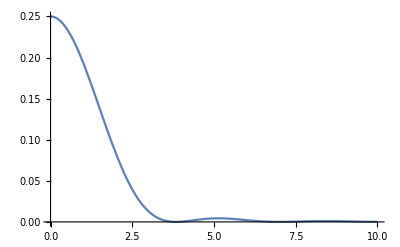

```mathematica
Plot[(BesselJ[1,k ]/k)^2,{k,0.0001,10}]
```

```mathematica
norm = Integrate[k(BesselJ[1,k ]/k)^2,{k,0,∞}]
```

1/2

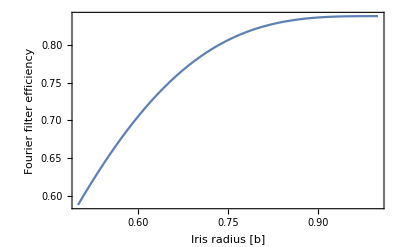

```mathematica
Plot[Integrate[k(BesselJ[1,k ]/k)^2,{k,0,α b}]/norm,{α,0.5,1},Frame->True,Axes->False,FrameLabel->{"Iris radius [b]","Fourier filter efficiency"}]
```

```mathematica
Integrate[k(BesselJ[1,k ]/k)^2,{k,0,α b}]/norm/.α->0.72
```

0.79276

```mathematica
α=1-BesselJ[0,BesselJZero[1,1]];
(-1-√(1-(1-α)^2))/α//N
```

-1.36538

The center of trap intensity (|A_2(0)/A_0|^2) as a function of the background and aperture transmission amplitudes, t_b and t_a (taken to be real), and relative phase between them, ϕ, is given below. This was derived by setting t_a -> t_a e^iϕ in Mark’s derivation.

```mathematica
η=tb^2+2tb(ta Cos[ϕ]-tb)α+(ta^2+tb^2-2ta tb Cos[ϕ])α^2;
NSolve[Evaluate[η/.{tb->1,ϕ->0}]==0,ta]
```

{{ta→0.287119},{ta→0.287119}}

```mathematica
Clear[α]
η=tb^2+2tb(ta Cos[ϕ]-tb)α+(ta^2+tb^2-2ta tb Cos[ϕ])α^2;
NSolve[Evaluate[η/.{tb->1,ϕ->0}]==0,ta]
```

{{ta→(-1.+α)/α},{ta→(-1.+α)/α}}

```mathematica
Collect[η/.tb->1,ta]
```

1-2 α+α^2+ta^2 α^2+ta (2 α Cos[ϕ]-2 α^2 Cos[ϕ])

```mathematica
NSolve[Evaluate[η/.{tb->1}]==0,ta]//TrigToExp//FullSimplify
```

{{ta→(ⅇ^(-ⅈ ϕ) (-1.+1. α))/α},{ta→(ⅇ^(ⅈ ϕ) (-1.+1. α))/α}}

```mathematica
α=1-BesselJ[0,BesselJZero[1,1]];
(ⅇ^(-ⅈ ϕ) (-1.+1. α))/α/.ϕ->0
```

0.287119

```mathematica
α//N
```

1.40276

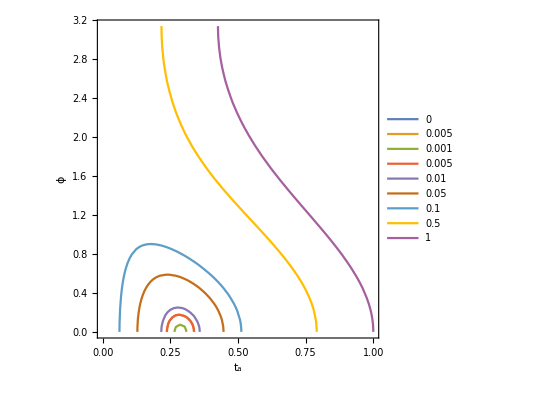

```mathematica
η=1-2 α+α^2+ta^2 α^2+ta (2 α Cos[ϕ]-2 α^2 Cos[ϕ]);
eff={0,0.005,0.001,0.005,.01,0.05,0.1,0.5,1};ContourPlot[Evaluate[Table[η==i,{i,eff}]],{ta,0,1},{ϕ,0,π},FrameLabel->{"t_a","ϕ"},LabelStyle->Directive[Black, Medium],PlotLegends->eff]
```

Repeat this, but find show that the optimal value of ta,phi depend on the choice of iris radius. Go back to where the assumption of b=x1 is made and let that be varied. Think about how to plot this.

## Trap depth, confinement, vibrational frequencies

## theory

### atom spatial distribution (std.)

Dark trap depth

1225

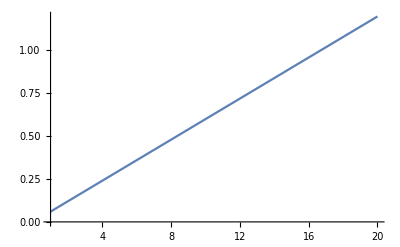

```mathematica
α0=-433*4*π*ϵ0*10^-30;(*Cs 6S1/2, 810 nm*)
d=3*^-6;
sites=1225
intensity = (P/sites)/d^2;(*P is total power illuminating the array mask*)
Plot[(-1/4 α0 2/(c ϵ0)intensity)/(kB 10^-3),{P,1,20}]
```

49

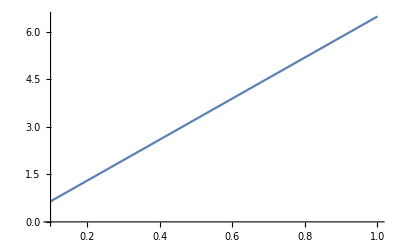

```mathematica
α0=-1370*4*π*ϵ0*10^-30;(*Rb 5S1/2, 770 nm*)
d=3λD2;
sites=49
intensity = (P/sites)/d^2;(*P is total power illuminating the array mask*)
Plot[(-1/4 α0 2/(c ϵ0)intensity)/(kB 10^-3),{P,.1,1}]
```

```mathematica
d
```

2.55704×10^-6

```mathematica
d
```

2.55704×10^-6

```mathematica
w0 = 10^-6;
λ = 8.08*^-7;
zR = π w0^2/λ;
```

Gaussian trap

```mathematica
"radial std, um"
σρ =w0/(√2)10^6//N
"axial std, um"
σz =zR/(√2)10^6//N
```

radial std, um

0.707107

axial std, um

2.74931

Airy-Gauss trap

```mathematica
"radial std, um"
σρ =w0/(√2)10^6//N
"axial std, um"
σz =(1.307zR)/(√2)10^6//N
```

radial std, um

0.707107

axial std, um

3.59335

Dark Airy-Gauss trap

```mathematica
"radial std, um"
σρ =(2/3)^(1/4)w0 10^6//N
"axial std, um"
σz =(0.997zR)/(√2)10^6//N
```

radial std, um

0.903602

axial std, um

2.74106

## experimental

Coherent dark trap:

```mathematica
Tfort = 0.001;
P = 0.150; (*watts*)
λ =8.25*^-7;
d0 = 430*^-6;
datoms  =3*^-6;
M = datoms/d0; (*3 um period at atoms, 430 um at mask*)
ωD2 =(2π c)/λD2;
Δ=c/λD2^2 Abs[λ-λD2]; (*freq detuning from wavelength detuning*)
Ufort = (3π)/2(c^2 ΓD2)/(ωD2^3 Δ)Ifort;
Ifort = kB Tfort((3π)/2(c^2 ΓD2)/(ωD2^3 Δ))^-1;
I0 = M^2 Ifort;
"radius of circular beam on mask, mm"
r = √(P/(π I0));
1000 r
"side of a square beam on mask, mm"
s = √(P/I0);
1000 s
"number of sites along row of a square:"
Floor[s/d0-1]
```

radius of circular beam on mask, mm

2.84648

side of a square beam on mask, mm

5.04525

number of sites along row of a square:

10

Trap depth for a given peak intensity with Gaussian illumination, and trap frequency estimate given a guess for the waist size.

```mathematica
1/mCorrect
```

1.23824

```mathematica
P = 0.26; (*power before JenOptik objective*)
h = 0.65;(*scaling factor; the axial intensity profile can be fit to (z/(h zR))^2. can estimate this factor from my numerical models*)
mThorcam =50/60;
(*magnification to the thorcam,from intermediate image*)
m4f = 75/275;
mAtoms=(30/200)(22.3/150);
(*magnification to the atoms, from intermediate image*)
mCorrect = 430*^-6*m4f*mThorcam/121.01*^-6;
(*center-to-center site period expected at Thorcam compared to measured*)
"Gaussian envelope at atoms, μm"
wTrap = 555.202*^-6/mThorcam*mAtoms*mCorrect;(*width of the Gaussian envelope of the entire array,at the atoms, from Thorcam fit image*)
wTrap*10^6
"Gaussian trap waist at atoms, μm"
w0=87.4047*^-6/mThorcam*mAtoms*mCorrect;(*estimated trap Gaussian waist, from Thorcam fit image*)
w0*10^6
zR = (π w0^2)/λ;
Ifort = (2P)/(π wTrap^2);
α0 = 10^-12(*Cs 6S1/2 polarizability at 825nm [K/(W/m^2)]*)
Ufort=kB*α0 Ifort;
"Maximum Trap depth, mK"
Ufort/kB/1*^-3
"Radial trap frequency, kHz"
2/(2π w0)√(Ufort/mCs)/1*^3
"Axial trap frequency, kHz"
1/(2π h zR)√((2Ufort)/mCs)/1*^3
```

Gaussian envelope at atoms, μm

11.9986

Gaussian trap waist at atoms, μm

1.88893

1/1000000000000

Maximum Trap depth, mK

1.14971

Radial trap frequency, kHz

5.71386 √(kB/mCs)

Axial trap frequency, kHz

1.04746×10^6 √(kB/mCs) λ

1.14971×10^9

```mathematica
2.15/1.15
```

1.86957

```mathematica
λ
```

4.17585×10^-9

```mathematica
(*measured trap resonances*)
"Site 0"
Clear[w]
fρ=78.2/2;
fz=10.2/2;
NSolve[{fρ==(2/(2π w))√((kB T)/mCs)/1*^3,fz==(λ/(2 h π^2 w^2))√((2kB T)/mCs)/1*^3},{T,w},Reals]
"Site 1"
fρ=103.5/2;
fz=15.5/2;
NSolve[{fρ==(2/(2π w))√((kB T)/mCs)/1*^3,fz==(λ/(2 h π^2 w^2))√((2kB T)/mCs)/1*^3},{T,w},Reals]
```

Site 0

{{T→0.00115694,w→2.19019×10^-6}}

Site 1

{{T→0.00153738,w→1.90759×10^-6}}

Error percentage

```mathematica
1-2.19/1.87
```

-0.121693

```mathematica
1-1.81/1.87
```

0.0320856

### Incoherent dark trap

The trap magnification optics are the same as for the coherent trap setup, so I will assume the trap waist should be the same, and solve for the trap depth and m^2 based on the trap frequencies.

```mathematica
λ =8.08*^-7;
NA=0.22;
rcore = 400*^-6;
"Maximum m^2 out of fiber"
msqMax = π rcore NA /λ
```

Maximum m^2 out of fiber

342.154

```mathematica
(*waist from coherent laser calibrated fit*)
(*w0=87.4047*^-6/mThorcam*mAtoms*mCorrect;*)
w0=1.59192*^-6; (*see projected image analysis nb*)

(*measured trap resonances*)
"Site 1"
fρ=68/2;
fz=12/2;
w=w0;
Clear[h]
NSolve[{fρ==(2/(2π w))√((kB T)/mCs)/1*^3,fz==(λ/(2  h π^2 w^2))√((2kB T)/mCs)/1*^3},{T,h},Reals]
```

Site 1

{{T→0.00046216,h→0.647371}}

```mathematica
1-0.435/0.385
```

-0.12987

```mathematica
"predicted lifetime from RIN measurement"
1/(π^2(fρ*1000)^2(10^(-110/20))^2)//N
```

predicted lifetime from RIN measurement

8.76481

```mathematica
1/(π^2(10*1000)^2(3*10^-6)^2)//N
```

112.579

```mathematica
α0=0.66*10^-6;
(*mK/W/m^2from yunheung*)(*-425(4π ϵ0*10^-30)*)
Itrap =0.9(0.4*30)/(π(.01)^2)(430/3)^2;(*the 0.9 comes from the traps going only 90% down or so*)(*power/(mask area)(1/magnification)^2*)
(*Et = √(2 Itrap/(c ϵ0));
1/4 α0 Et^2/kB *)
α0 Itrap/10^3
```

0.466136

```mathematica
Itrap
```

7.06266×10^8

```mathematica
1-462/466//N
```

0.00858369

## Effect of spectral incoherence

```mathematica
ZT = (2 d^2)/λ;
dZT=Δλ D[ZT,λ];
zR = π/λ(a f2/f1)^2;
Solve[dZT/zR==1/2,Δλ]
```

{{Δλ→-(a^2 f2^2 π λ)/(4 d^2 f1^2)}}

## Gaussian dark trap

## Expansion in ρ,z, assuming|1-Eg|^2

```mathematica
Clear[w,w0,R,η,λ]
zR = π w0^2/λ;
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
Iexac=(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2]);
(*Assuming[ρ∈Reals&&λ∈Reals&&w0∈Reals&&z∈Reals&&R∈Reals,(1-Eg)conj[1-Eg]//FullSimplify]*)
```

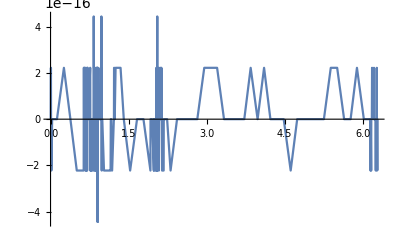

```mathematica
(*check my exact form for the intensity*)
Iexpr  =(1-Eg)conj[1-Eg];
λ = w0=1;
Plot[{Iexpr-Iexac/.ρ->0.001},{z,0,2zR}]
```

```mathematica
Series[(1-Eg)(1-Egc),{z,0,4}]//FullSimplify
```

(-1+ⅇ^(-ρ^2/w0^2))^2+(ⅇ^(-(2 ρ^2)/w0^2) λ^2 (-w0^4+2 w0^2 ρ^2+ⅇ^(ρ^2/w0^2) (2 w0^4-4 w0^2 ρ^2+ρ^4)) z^2)/(π^2 w0^8)+1/(12 π^4 w0^16)ⅇ^(-(2 ρ^2)/w0^2) λ^4 (12 w0^4 (w0^4-4 w0^2 ρ^2+2 ρ^4)-ⅇ^(ρ^2/w0^2) (24 w0^8-96 w0^6 ρ^2+72 w0^4 ρ^4-16 w0^2 ρ^6+ρ^8)) z^4+O[z]^5

```mathematica
%/.ρ->0
```

(λ^2 z^2)/(π^2 w0^4)-(λ^4 z^4)/(π^4 w0^8)+O[z]^5

```mathematica
Series[(1-Eg)(1-Egc),{ρ,0,6}]//FullSimplify
```

(z^2 λ^2)/(π^2 w0^4+z^2 λ^2)-(2 (π^2 w0^2 z^2 λ^2) ρ^2)/((π^2 w0^4+z^2 λ^2)^2)+((π^6 w0^8+3 π^4 w0^4 z^2 λ^2) ρ^4)/((π^2 w0^4+z^2 λ^2)^3)+((-3 π^8 w0^10-6 π^6 w0^6 z^2 λ^2+π^4 w0^2 z^4 λ^4) ρ^6)/(3 (π^2 w0^4+z^2 λ^2)^4)+O[ρ]^7

```mathematica
%/.z-> 0
```

ρ^4/w0^4-ρ^6/w0^6+O[ρ]^7

```mathematica
Series[(w0/w)^2 Exp[(-2 ρ^2)/w^2],{ρ,0,5}]/.z->0
Series[(w0/w)^2 Exp[(-2 ρ^2)/w^2]//ComplexExpand,{z,0,5}]/.ρ->0
```

1-(2 ρ^2)/w0^2+(2 ρ^4)/w0^4+O[ρ]^6

1-(λ^2 z^2)/(π^2 w0^4)+(λ^4 z^4)/(π^4 w0^8)+O[z]^6

## Exact profile of Gaussian dark trap

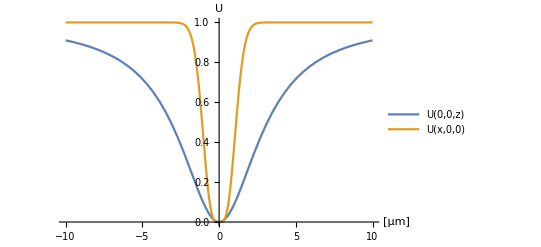
```mathematica
Iexpr  =(1-Eg)conj[1-Eg];
λ =w0=1;
Plot[{(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])/.{ρ->0.001,z->x},(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])/.{z->0.001,ρ->x}},{x,-10,10},PlotRange->All,PlotLegends->{"U(0,0,z)","U(x,0,0)"},AxesLabel->{"[μm]","U"}]
-Graphics-
Plot3D[Iexpr,{ρ,-100,100},{z,-100,100},AxesLabel->{"x","z","U"},PlotRange->All]
-Graphics3D-
```

## Rotated slices

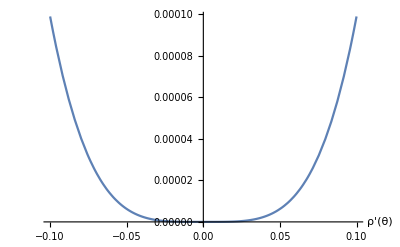
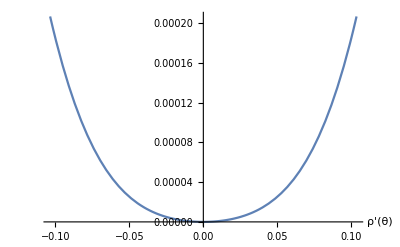
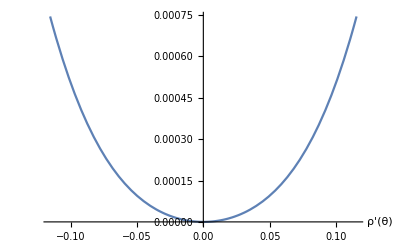
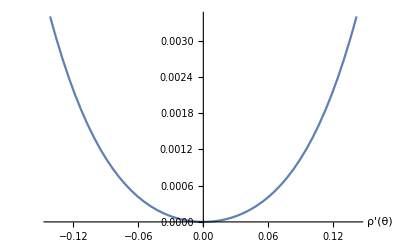
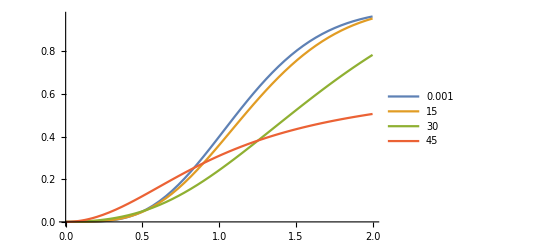
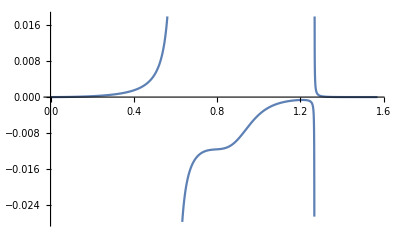
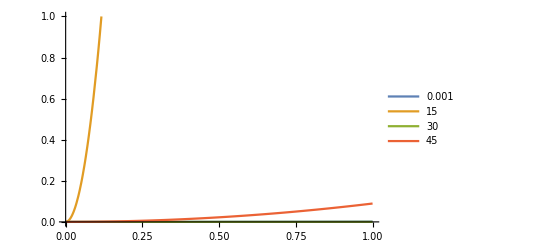
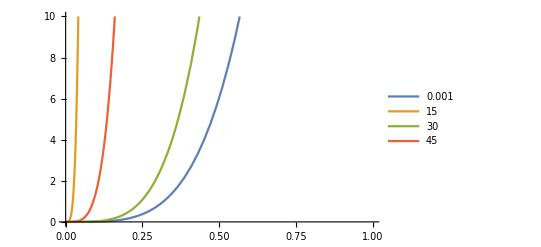
```mathematica
({{ρρ}, {zz}})=({{Cos[x], -Sin[x]}, {Sin[x], Cos[x]}}).({{ρ}, {z}})
{{ρ Cos[x]-z Sin[x]},{z Cos[x]+ρ Sin[x]}}
Work in units with zR=w0=λ=1;
w0=λ=1;
zR = π w0^2/λ;
w=w0(1+(zz/zR)^2)^(1/2);
R=zz(1+zR^2/zz^2);
η=ArcTan[zz/zR];
Idark= 1-2 w0/w Cos[η-π/(R λ)ρρ^2]Exp[-ρρ^2/w^2]+(w0/w)^2 Exp[(-2 ρρ^2)/w^2];
xvals ={0.001,15,30,45};
plts = Table[Plot[Idark/.{ρρ->ρ (Cos[x/180 π]+Tan[x/180 π]Sin[x/180 π]),zz->-ρ Tan[x/180 π]},{ρ,-0.1w0 (Cos[x/180 π]+Tan[x/180 π]Sin[x/180 π]),0.1w0 (Cos[x/180 π]+Tan[x/180 π]Sin[x/180 π])},PlotLegends->StringForm["θ=``",x],AxesLabel->{"ρ'(θ)"}],{x,xvals}]
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
Plot3D[Idark/.{ρρ->ρ,zz->z},{ρ,-2w0,2 w0},{z,-2zR,2zR},AxesLabel->{"x","z","U"},PlotRange->All,LabelStyle->Directive[Bold, Medium]]
-Graphics3D-
x=45;(*rotate by 45 degrees*)
Plot3D[Idark/.{ρρ->(ρ +z Sin[x/180 π])/Cos[x/180 π],zz->(z -ρ Sin[x/180 π])/Cos[x/180 π]},{ρ,-10,10},{z,-10,10},AxesLabel->{"x","z","U"},PlotRange->All]
-Graphics3D-
Clear[x];
z = -ρ Tan[x/180 π];
xvals = {0.001,15,30,45};
Plot[Evaluate[Table[Idark/.{ρρ->(ρ + z Sin[x/180 π])/Cos[x/180 π],zz->(z -ρ Sin[x/180 π])/Cos[x/180 π]},{x,xvals}]],{ρ,0,2w0},PlotRange->All,PlotLegends->xvals]
-Graphics-
Collect[Series[Idark/.{ρρ->(ρ -ρ Tan[θ] Sin[θ])/Cos[θ],zz->(-ρ Tan[θ]-ρ Sin[θ])/Cos[θ]},{ρ,0,4}],ρ]
(ρ^2 (Tan[θ]^2+2 Sec[θ] Tan[θ]^2+Sec[θ]^2 Tan[θ]^2))/π^2+1/π^4 ρ^4 (π^4 Sec[θ]^4-2 π^2 Sec[θ]^2 Tan[θ]^2-4 π^2 Sec[θ]^3 Tan[θ]^2-4 π^4 Sec[θ]^3 Tan[θ]^2-2 π^2 Sec[θ]^4 Tan[θ]^2-Tan[θ]^4-4 Sec[θ] Tan[θ]^4+4 π^2 Sec[θ] Tan[θ]^4-6 Sec[θ]^2 Tan[θ]^4+8 π^2 Sec[θ]^2 Tan[θ]^4+6 π^4 Sec[θ]^2 Tan[θ]^4-4 Sec[θ]^3 Tan[θ]^4+4 π^2 Sec[θ]^3 Tan[θ]^4-Sec[θ]^4 Tan[θ]^4-2 π^2 Tan[θ]^6-4 π^2 Sec[θ] Tan[θ]^6-4 π^4 Sec[θ] Tan[θ]^6-2 π^2 Sec[θ]^2 Tan[θ]^6+π^4 Tan[θ]^8)
%/.θ->0
ρ^4
Plot[(Tan[θ]^2+2 Sec[θ] Tan[θ]^2+Sec[θ]^2 Tan[θ]^2)/π^2/(π^4 Sec[θ]^4-2 π^2 Sec[θ]^2 Tan[θ]^2-4 π^2 Sec[θ]^3 Tan[θ]^2-4 π^4 Sec[θ]^3 Tan[θ]^2-2 π^2 Sec[θ]^4 Tan[θ]^2-Tan[θ]^4-4 Sec[θ] Tan[θ]^4+4 π^2 Sec[θ] Tan[θ]^4-6 Sec[θ]^2 Tan[θ]^4+8 π^2 Sec[θ]^2 Tan[θ]^4+6 π^4 Sec[θ]^2 Tan[θ]^4-4 Sec[θ]^3 Tan[θ]^4+4 π^2 Sec[θ]^3 Tan[θ]^4-Sec[θ]^4 Tan[θ]^4-2 π^2 Tan[θ]^6-4 π^2 Sec[θ] Tan[θ]^6-4 π^4 Sec[θ] Tan[θ]^6-2 π^2 Sec[θ]^2 Tan[θ]^6+π^4 Tan[θ]^8),{θ,0,π/2}]
-Graphics-
Plot[Evaluate[Table[(ρ^2 (Tan[θ]^2+2 Sec[θ] Tan[θ]^2+Sec[θ]^2 Tan[θ]^2))/π^2,{θ,xvals*180/π}]],{ρ,0,1},PlotLegends->xvals,PlotTheme->"Monochromatic",PlotRange->{0,1}]
-Graphics-
Plot[Evaluate[Table[ρ^4 (π^4 Sec[θ]^4-2 π^2 Sec[θ]^2 Tan[θ]^2-4 π^2 Sec[θ]^3 Tan[θ]^2-4 π^4 Sec[θ]^3 Tan[θ]^2-2 π^2 Sec[θ]^4 Tan[θ]^2-Tan[θ]^4-4 Sec[θ] Tan[θ]^4+4 π^2 Sec[θ] Tan[θ]^4-6 Sec[θ]^2 Tan[θ]^4+8 π^2 Sec[θ]^2 Tan[θ]^4+6 π^4 Sec[θ]^2 Tan[θ]^4-4 Sec[θ]^3 Tan[θ]^4+4 π^2 Sec[θ]^3 Tan[θ]^4-Sec[θ]^4 Tan[θ]^4-2 π^2 Tan[θ]^6-4 π^2 Sec[θ] Tan[θ]^6-4 π^4 Sec[θ] Tan[θ]^6-2 π^2 Sec[θ]^2 Tan[θ]^6+π^4 Tan[θ]^8),{θ,xvals*180/π}]],{ρ,0,1},PlotLegends->xvals,PlotTheme->"Monochromatic",PlotRange->{0,10}]
-Graphics-
```

## forces

for simulating dynamics by numerically solving the ODE

```mathematica
Clear[x,zR,w0,λ];
w=w0(1+(z/zR)^2)^(1/2);
R=z(1+zR^2/z^2);
η=ArcTan[z/zR];
Eg = w0/w Exp[-ⅈ η+ⅈ π/(λ R)ρ^2-ρ^2/w^2];
```

Bright trap:

```mathematica
fx=D[Eg conj[Eg]/.{ρ-> √(x^2+y^2)},x]
fy=D[Eg conj[Eg]/.{ρ-> √(x^2+y^2)},y]
fz=D[Eg conj[Eg]/.{ρ-> √(x^2+y^2)},z]
```

-(4 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) x)/(w0^2 (1+z^2/zR^2)^2)

-(4 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) y)/(w0^2 (1+z^2/zR^2)^2)

(4 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) (x^2+y^2) z)/(w0^2 (1+z^2/zR^2)^3 zR^2)-(2 ⅇ^(-(2 (x^2+y^2))/(w0^2 (1+z^2/zR^2))) z)/((1+z^2/zR^2)^2 zR^2)

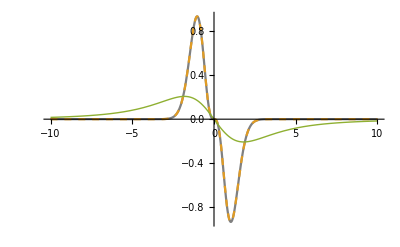

```mathematica
w0=λ=1;
zR = (π w0)/λ;
Plot[{fx/.{x->u,y->0,z->0},fy/.{x->0,y->u,z->0},fz/.{x->0,y->0,z->u}},{u,-10w0,10w0},PlotStyle->{Gray,Dashed,Thick},PlotRange->All]
```

Dark trap, Gaussian approximation. I = |1-Eg|^2, which is given exactly by the expression below.

```mathematica
Clear[zR,λ,w0]
Idark=(1-2 w0/w Cos[η-π/(R λ)ρ^2]Exp[-ρ^2/w^2]+(w0/w)^2 Exp[(-2 ρ^2)/w^2])
```

1+(ⅇ^(-(2 ρ^2)/(w0^2 (1+z^2/zR^2))))/(1+z^2/zR^2)-(2 ⅇ^(-ρ^2/(w0^2 (1+z^2/zR^2))) Cos[(π ρ^2)/(z (1+zR^2/z^2) λ)-ArcTan[z/zR]])/(√(1+z^2/zR^2))

```mathematica
fx=-D[Idark/.{ρ-> √(x^2+y^2)},x]//FullSimplify
fy=-D[Idark/.{ρ-> √(x^2+y^2)},y]//FullSimplify
fz=-D[Idark/.{ρ-> √(x^2+y^2)},z]//FullSimplify
```

(4 ⅇ^(-(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) x (zR^4-1/λ ⅇ^(((x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) √(1+z^2/zR^2) zR^2 (zR^2 λ Cos[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]]+π w0^2 z Sin[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]])))/(w0^2 (z^2+zR^2)^2)

(4 ⅇ^(-(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) y (zR^4-1/λ ⅇ^(((x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) √(1+z^2/zR^2) zR^2 (zR^2 λ Cos[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]]+π w0^2 z Sin[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]])))/(w0^2 (z^2+zR^2)^2)

(2 ⅇ^(-(2 (x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) zR^2 (-2 (x^2+y^2) z zR^2+w0^2 z (z^2+zR^2)+1/λ ⅇ^(((x^2+y^2) zR^2)/(w0^2 (z^2+zR^2))) √(1+z^2/zR^2) (-z (-2 (x^2+y^2) zR^2+w0^2 (z^2+zR^2)) λ Cos[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]]+w0^2 (π (x^2+y^2) (z-zR) (z+zR)+zR (z^2+zR^2) λ) Sin[(π (x^2+y^2) z)/((z^2+zR^2) λ)-ArcTan[z/zR]])))/(w0^2 (z^2+zR^2)^3)

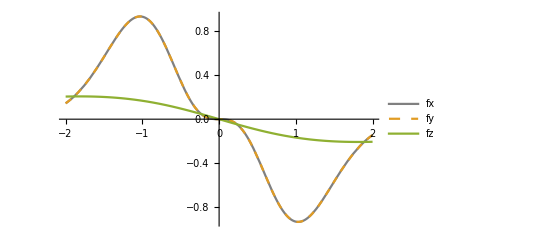

```mathematica
w0=λ=1;
Plot[{fx/.{x->u,y->0,z->0},fy/.{x->0,y->u,z->0},fz/.{x->0,y->0,z->u}},{u,-2w0,2w0},PlotStyle->{Gray,Dashed,Thick},PlotRange->All,PlotLegends->{"fx","fy","fz"}]
```

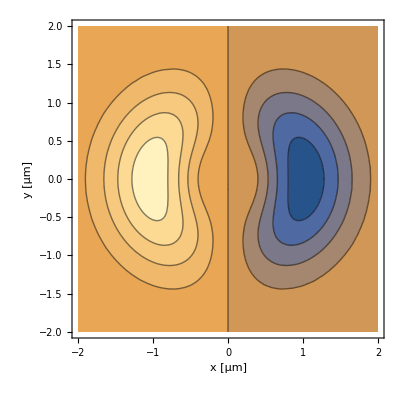
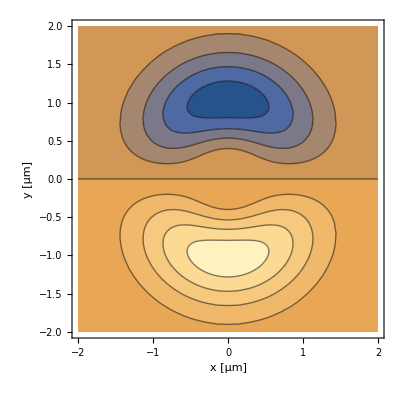
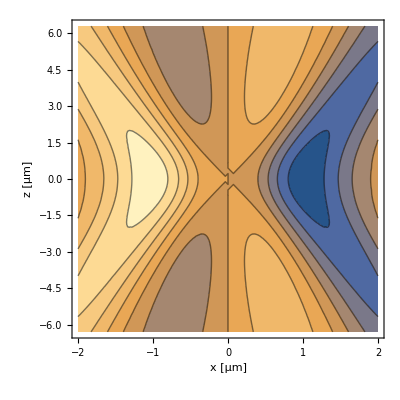
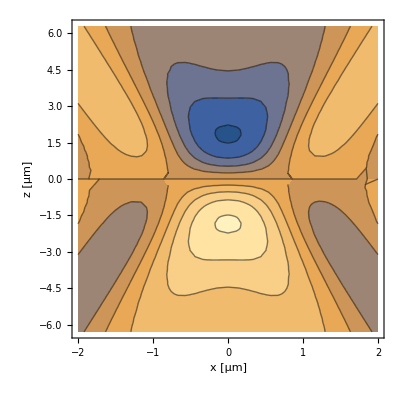
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
w0=λ=1;
GridBox[{{ContourPlot[fx/.z->0,{x,-2w0,2w0},{y,-2w0,2w0},FrameLabel->{"x [μm]","y [μm]"},PlotLegends->"fx"],ContourPlot[fy/.z->0,{x,-2w0,2w0},{y,-2w0,2w0},FrameLabel->{"x [μm]","y [μm]"},PlotLegends->"fy"]},{ContourPlot[fx/.y->0,{x,-2w0,2w0},{z,-2zR,2zR},FrameLabel->{"x [μm]","z [μm]"},PlotLegends->"fx"],ContourPlot[fz/.y->0,{x,-2w0,2w0},{z,-2zR,2zR},FrameLabel->{"x [μm]","z [μm]"},PlotLegends->"fz"]}}]//DisplayForm
```

```mathematica
SetAttributes[withname,HoldFirst];
withname[x_]:={x,SymbolName[Unevaluated@x]};
```

```mathematica
withname[fy]
```

{1/((π^2+z^2)^2)4 ⅇ^(-(2 π^2 (x^2+y^2))/(π^2+z^2)) y (π^4-ⅇ^((π^2 (x^2+y^2))/(π^2+z^2)) π^2 √(1+z^2/π^2) (π^2 Cos[(π (x^2+y^2) z)/(π^2+z^2)-ArcTan[z/π]]+π z Sin[(π (x^2+y^2) z)/(π^2+z^2)-ArcTan[z/π]])),fy}

```mathematica
w0=λ=1;
GridBox[{Table[ContourPlot3D[f[[1]],{x,-2w0,2w0},{y,-2w0,2w0},{z,-2zR,2zR},PlotLegends->f[[2]]],{f,{withname[fx],withname[fy],withname[fz]}}]}]//DisplayForm
```

-Graphics3D- | -Graphics3D- | -Graphics3D-

## misc analysis

## fit Fresnel calculation from python

```mathematica
(*from 35x35 mask with b = 0.4*x11*f/ka, ta=0.7, phi=160 deg, a=100um, d=430um,f1=0.5m,f2=0.05m *)
zpts={0.00019444,0.00038889,0.00058333,0.00077778,0.00097222,0.00116667,0.00136111,0.00155556,0.00175,0.00194444,0.00213889,0.00233333,0.00252778};
ipts = {0.01502224,0.0408047,0.0980485,0.18274581,0.28894299,0.40915869,0.53491028,0.657312,0.76770249,0.85825762,0.92254535,0.95598325,0.95616622};
```

```mathematica
iz= Fit[Transpose@@{{zpts,ipts}},{1,z^2,z^4,z^6,z^8},z]
```

-0.00562828+326996. z^2-1.10598×10^10 z^4-5.81525×10^15 z^6+5.05291×10^20 z^8

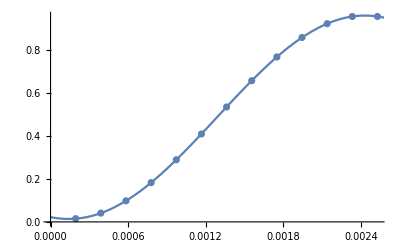

```mathematica
Show[ListPlot[Transpose@@{{zpts,ipts}}],Plot[{iz},{z,0,0.003}]]
```

```mathematica
(*radial fit to get the waist*)
```

3.73399-1.44845×10^9 x^2+2.1113×10^17 x^4-1.42862×10^25 x^6+4.09251×10^32 x^8

0.0000262754

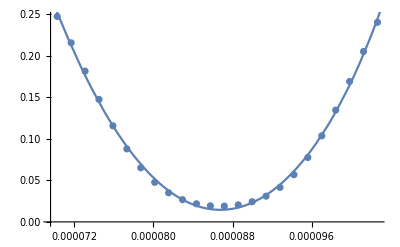

```mathematica
ixpts = {0.24701732,0.21539315,0.18128151,0.14724851,0.11552849,0.08779616,0.06503956,0.04754862,0.035015,0.02672049,0.02177698,0.01937291,0.01898123,0.02049081,0.02423764,0.03092969,0.04147853,0.05676759,0.07739868,0.10346329,0.13438197,0.16884466,0.2048685,0.23997038};
xpts = {7.02997275*^-5,7.17057221*^-5,7.31117166*^-5,7.45177112*^-5,7.59237057*^-5,7.73297003*^-5,7.87356948*^-5,8.01416894*^-5,8.15476839*^-5,8.29536785*^-5,8.43596730*^-5,8.57656676*^-5,8.71716621*^-5,8.85776567*^-5,8.99836512*^-5,9.13896458*^-5,9.27956403*^-5,9.42016349*^-5,9.56076294*^-5,9.70136240*^-5,9.84196185*^-5,9.98256131*^-5,1.01231608*^-4,1.02637602*^-4};
ix = Fit[Transpose@@{{xpts,ixpts}},{1,x^2,x^4,x^6,x^8},x]
w0=(Abs[ix[[2]]/x^2])^(-1/2)
Show[ListPlot[Transpose@@{{xpts,ixpts}}],Plot[{ix},{x,-10^-4,1.2*10^-4}]]
```

```mathematica
(1.448445778900827*^9)^(-1/2)
```

0.0000262754

```mathematica
zR = π*w0^2/(8.08*^-7)
```

0.00268433

```mathematica
zR
```

0.000345838

```mathematica
Array[iz[[#]] zR^#&,Length[iz]]
(%[[2]]/z^2)^(-1/2)//N
```

{-0.0000151082,2.35621 z^2,-213.922 z^4,-301935. z^6,7.04243×10^7 z^8}

0.651467

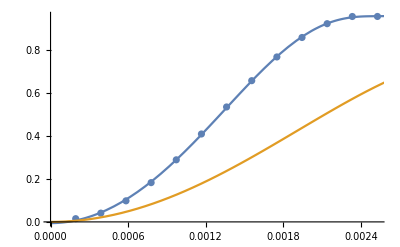

```mathematica
Show[ListPlot[Transpose@@{{zpts,ipts}}],Plot[{iz,1.0068(z/zR)^2-0.33009(z/zR)^4},{z,0,0.003}]]
```

```mathematica
0.03910992090232635^(-1/2)
```

5.05658

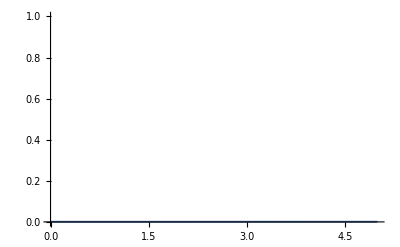

```mathematica
Plot[7.747285672215779*^-6-0.00001470867615301061 z+0.000017828191052678082 z^2+6.704981849370443*^-7 z^3-3.727680174319587*^-7 z^4,{z,0,5},PlotRange->{0,1}]
```